## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

```mathematica
1
```

1

### DataToEquations and the critical congestion solver

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
```

```mathematica
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Iterative DNF convertion took 129.709 seconds to terminate

Iterative DNF convertion took 0.269787 seconds to terminate

Iterative DNF convertion took 0.056935 seconds to terminate

Iterative DNF convertion took 0.063122 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{131.78,Null}

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

All restrictions are True

Nrhs: {-63.8483,-166.281,14.8433,-98.5123,-126.218,1.61986,-108.215,-116.133,-0.0741253,-14.8433,-74.3894,-16.033,-76.1845,-42.5055}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->4],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,3->5],j10-j9-IntM[j10-j9,4->6],-j11+j12-IntM[-j11+j12,5->6],-j13+j14-IntM[-j13+j14,5->7],-j15+j16-IntM[-j15+j16,6->8],-j17+j18-IntM[-j17+j18,7->8],-j19+j20-IntM[-j19+j20,7->9],-j21+j22-IntM[-j21+j22,7->10],-j23+j24-IntM[-j23+j24,8->9],-j25+j26-IntM[-j25+j26,8->11],-j27+j28-IntM[-j27+j28,9->12]}

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Max error for non-linear solution: 166.281

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
Get[dddRicardo]
alpha[edge_]:=0.2
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative boolean convert took 138.446 seconds to terminate

Iterative boolean convert took 0.639312 seconds to terminate

Iterative boolean convert took 0.576127 seconds to terminate

Iterative boolean convert took 0.047569 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {443102620248673769/26000000000000000≤jt30≤230959458548939067/13000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→1833899905342459641/26000000000000000,j3→0,j5→481899905342459641/26000000000000000,j10→2222100094657540359/26000000000000000,j7→0,j12→0,j14→980290582045287743/13000000000000000,j9→0,j11→25336251749623169/5200000000000000,j16→1047709417954712257/13000000000000000,j13→0,j18→0,j20→230959458548939067/13000000000000000,j22→1517478543841901717/26000000000000000,j15→0,j17→3763259369840873/5200000000000000,j24→509941369210967137/26000000000000000,j26→391665292462313253/6500000000000000,j19→0,j23→0,j28→74758483562218867/2000000000000000,j21→0,j30→1517478543841901717/26000000000000000,j25→0,j32→391665292462313253/6500000000000000,j27→0,j34→74758483562218867/2000000000000000,u30→0,u32→0,u34→0,jt12→2222100094657540359/26000000000000000,jt13→0,jt14→0,jt2→52,jt20→25336251749623169/5200000000000000,jt23→25336251749623169/5200000000000000,jt24→1047709417954712257/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→230959458548939067/13000000000000000,jt55→0,jt56→509941369210967137/26000000000000000,jt58→0,jt59→1517478543841901717/26000000000000000,jt6→52,jt60→0,jt61→391665292462313253/6500000000000000,jt62→0,jt63→74758483562218867/2000000000000000,jt64→0,jt7→0,jt8→481899905342459641/26000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→36733357583234587/1300000000000000,u38→894131773540328621/26000000000000000,jt1→0,jt35→0,jt39→0,jt43→391665292462313253/6500000000000000,jt57→0,u10→218656208373973427/13000000000000000,u13→377456850288871603/26000000000000000,u14→190086456153577813/26000000000000000,u15→218656208373973427/13000000000000000,u16→10729855400604929/1300000000000000,u17→190086456153577813/26000000000000000,u18→10729855400604929/1300000000000000,u2→1124633799462587/52000000000000,u20→8478369835886147/2000000000000000,u21→190086456153577813/26000000000000000,u25→10729855400604929/1300000000000000,u27→8478369835886147/2000000000000000,u35→36733357583234587/1300000000000000,u37→894131773540328621/26000000000000000,u4→662165536262932909/26000000000000000,u7→1124633799462587/52000000000000,u8→377456850288871603/26000000000000000,u9→662165536262932909/26000000000000000,jt15→0,jt21→0,jt31→980290582045287743/13000000000000000-jt30,jt36→0,jt49→0,u11→377456850288871603/26000000000000000,u12→218656208373973427/13000000000000000,u19→190086456153577813/26000000000000000,u22→0,u23→10729855400604929/1300000000000000,u24→8478369835886147/2000000000000000,u26→0,u28→0,u3→894131773540328621/26000000000000000,u5→1124633799462587/52000000000000,u6→662165536262932909/26000000000000000,jt10→0,jt11→481899905342459641/26000000000000000,jt16→0,jt17→0,jt18→1833899905342459641/26000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→230959458548939067/13000000000000000-jt30,jt34→-443102620248673769/26000000000000000+jt30,jt37→0,jt41→3763259369840873/5200000000000000,jt42→509941369210967137/26000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→36733357583234587/1300000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.315 seconds to terminate

Iterative boolean convert took 0.621953 seconds to terminate

Iterative boolean convert took 0.572187 seconds to terminate

Iterative boolean convert took 0.044054 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {837541520173026301/52000000000000000≤jt30≤866227980057265751/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→1822278183688167369/26000000000000000,j3→0,j5→470278183688167369/26000000000000000,j10→2233721816311832631/26000000000000000,j7→0,j12→0,j14→486383955208188721/6500000000000000,j9→0,j11→24651527428917503/5200000000000000,j16→527616044791811279/6500000000000000,j13→0,j18→0,j20→866227980057265751/52000000000000000,j22→3053530121492483467/52000000000000000,j15→0,j17→573729197684789/1040000000000000,j24→999092407078788877/52000000000000000,j26→638629898274292381/10400000000000000,j19→0,j23→0,j28→35871545906462589/1000000000000000,j21→0,j30→3053530121492483467/52000000000000000,j25→0,j32→638629898274292381/10400000000000000,j27→0,j34→35871545906462589/1000000000000000,u30→0,u32→0,u34→0,jt12→2233721816311832631/26000000000000000,jt13→0,jt14→0,jt2→52,jt20→24651527428917503/5200000000000000,jt23→24651527428917503/5200000000000000,jt24→527616044791811279/6500000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→866227980057265751/52000000000000000,jt55→0,jt56→999092407078788877/52000000000000000,jt58→0,jt59→3053530121492483467/52000000000000000,jt6→52,jt60→0,jt61→638629898274292381/10400000000000000,jt62→0,jt63→35871545906462589/1000000000000000,jt64→0,jt7→0,jt8→470278183688167369/26000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→58766289825352013/2080000000000000,u38→1786676213393929463/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→638629898274292381/10400000000000000,jt57→0,u10→872997355262315593/52000000000000000,u13→150977714253090039/10400000000000000,u14→76152031151947983/10400000000000000,u15→872997355262315593/52000000000000000,u16→85399871526759389/10400000000000000,u17→76152031151947983/10400000000000000,u18→85399871526759389/10400000000000000,u2→224891348353400769/10400000000000000,u20→4246611609607153/1000000000000000,u21→76152031151947983/10400000000000000,u25→85399871526759389/10400000000000000,u27→4246611609607153/1000000000000000,u35→58766289825352013/2080000000000000,u37→1786676213393929463/52000000000000000,u4→1322743738839138039/52000000000000000,u7→224891348353400769/10400000000000000,u8→150977714253090039/10400000000000000,u9→1322743738839138039/52000000000000000,jt15→0,jt21→0,jt31→486383955208188721/6500000000000000-jt30,jt36→0,jt49→0,u11→150977714253090039/10400000000000000,u12→872997355262315593/52000000000000000,u19→76152031151947983/10400000000000000,u22→0,u23→85399871526759389/10400000000000000,u24→4246611609607153/1000000000000000,u26→0,u28→0,u3→1786676213393929463/52000000000000000,u5→224891348353400769/10400000000000000,u6→1322743738839138039/52000000000000000,jt10→0,jt11→470278183688167369/26000000000000000,jt16→0,jt17→0,jt18→1822278183688167369/26000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→866227980057265751/52000000000000000-jt30,jt34→-837541520173026301/52000000000000000+jt30,jt37→0,jt41→573729197684789/1040000000000000,jt42→999092407078788877/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→58766289825352013/2080000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.382 seconds to terminate

Iterative boolean convert took 0.653473 seconds to terminate

Iterative boolean convert took 0.577644 seconds to terminate

Iterative boolean convert took 0.045508 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {790627679985476237/52000000000000000≤jt30≤814390394100597087/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→1811140147605500293/26000000000000000,j3→0,j5→459140147605500293/26000000000000000,j10→2244859852394499707/26000000000000000,j7→0,j12→0,j14→96549501917609847/1300000000000000,j9→0,j11→119849890746696647/26000000000000000,j16→106250498082390153/1300000000000000,j13→0,j18→0,j20→814390394100597087/52000000000000000,j22→3071352396718917643/52000000000000000,j15→0,j17→475254282302417/1040000000000000,j24→978109598600969789/52000000000000000,j26→3248147610579515481/52000000000000000,j19→0,j23→0,j28→34471153705799363/1000000000000000,j21→0,j30→3071352396718917643/52000000000000000,j25→0,j32→3248147610579515481/52000000000000000,j27→0,j34→34471153705799363/1000000000000000,u30→0,u32→0,u34→0,jt12→2244859852394499707/26000000000000000,jt13→0,jt14→0,jt2→52,jt20→119849890746696647/26000000000000000,jt23→119849890746696647/26000000000000000,jt24→106250498082390153/1300000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→814390394100597087/52000000000000000,jt55→0,jt56→978109598600969789/52000000000000000,jt58→0,jt59→3071352396718917643/52000000000000000,jt6→52,jt60→0,jt61→3248147610579515481/52000000000000000,jt62→0,jt63→34471153705799363/1000000000000000,jt64→0,jt7→0,jt8→459140147605500293/26000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→1468920125725063469/52000000000000000,u38→1785100829415244247/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→3248147610579515481/52000000000000000,jt57→0,u10→174286955964117613/10400000000000000,u13→754752865883703267/52000000000000000,u14→380957660427455339/52000000000000000,u15→174286955964117613/10400000000000000,u16→425158693142522553/52000000000000000,u17→380957660427455339/52000000000000000,u18→425158693142522553/52000000000000000,u2→1124219621858266989/52000000000000000,u20→4253272374020519/1000000000000000,u21→380957660427455339/52000000000000000,u25→425158693142522553/52000000000000000,u27→4253272374020519/1000000000000000,u35→1468920125725063469/52000000000000000,u37→1785100829415244247/52000000000000000,u4→1321168354860452823/52000000000000000,u7→1124219621858266989/52000000000000000,u8→754752865883703267/52000000000000000,u9→1321168354860452823/52000000000000000,jt15→0,jt21→0,jt31→96549501917609847/1300000000000000-jt30,jt36→0,jt49→0,u11→754752865883703267/52000000000000000,u12→174286955964117613/10400000000000000,u19→380957660427455339/52000000000000000,u22→0,u23→425158693142522553/52000000000000000,u24→4253272374020519/1000000000000000,u26→0,u28→0,u3→1785100829415244247/52000000000000000,u5→1124219621858266989/52000000000000000,u6→1321168354860452823/52000000000000000,jt10→0,jt11→459140147605500293/26000000000000000,jt16→0,jt17→0,jt18→1811140147605500293/26000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→814390394100597087/52000000000000000-jt30,jt34→-790627679985476237/52000000000000000+jt30,jt37→0,jt41→475254282302417/1040000000000000,jt42→978109598600969789/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→1468920125725063469/52000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.659 seconds to terminate

Iterative boolean convert took 0.623415 seconds to terminate

Iterative boolean convert took 0.580631 seconds to terminate

Iterative boolean convert took 0.051722 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {149220976628042103/10400000000000000≤jt30≤153508560176812119/10400000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→90024890589540131/1300000000000000,j3→0,j5→22424890589540131/1300000000000000,j10→112775109410459869/1300000000000000,j7→0,j12→0,j14→958537142949318833/13000000000000000,j9→0,j11→58288237053917523/13000000000000000,j16→1069462857050681167/13000000000000000,j13→0,j18→0,j20→153508560176812119/10400000000000000,j22→3088043688657064817/52000000000000000,j15→0,j17→133986985899063/325000000000000,j24→957420805641493267/52000000000000000,j26→3298992704817381321/52000000000000000,j19→0,j23→0,j28→66344754097136687/2000000000000000,j21→0,j30→3088043688657064817/52000000000000000,j25→0,j32→3298992704817381321/52000000000000000,j27→0,j34→66344754097136687/2000000000000000,u30→0,u32→0,u34→0,jt12→112775109410459869/1300000000000000,jt13→0,jt14→0,jt2→52,jt20→58288237053917523/13000000000000000,jt23→58288237053917523/13000000000000000,jt24→1069462857050681167/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→153508560176812119/10400000000000000,jt55→0,jt56→957420805641493267/52000000000000000,jt58→0,jt59→3088043688657064817/52000000000000000,jt6→52,jt60→0,jt61→3298992704817381321/52000000000000000,jt62→0,jt63→66344754097136687/2000000000000000,jt64→0,jt7→0,jt8→22424890589540131/1300000000000000,jt9→0,u29→0,u31→0,u33→0,u36→293725154812191593/10400000000000000,u38→1783557443176569101/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→3298992704817381321/52000000000000000,jt57→0,u10→869970619164108741/52000000000000000,u13→30179803154766973/2080000000000000,u14→380733515945151217/52000000000000000,u15→869970619164108741/52000000000000000,u16→423724727300789833/52000000000000000,u17→380733515945151217/52000000000000000,u18→423724727300789833/52000000000000000,u2→224785054038832297/10400000000000000,u20→1703687619317779/400000000000000,u21→380733515945151217/52000000000000000,u25→423724727300789833/52000000000000000,u27→1703687619317779/400000000000000,u35→293725154812191593/10400000000000000,u37→1783557443176569101/52000000000000000,u4→1319624968621777677/52000000000000000,u7→224785054038832297/10400000000000000,u8→30179803154766973/2080000000000000,u9→1319624968621777677/52000000000000000,jt15→0,jt21→0,jt31→958537142949318833/13000000000000000-jt30,jt36→0,jt49→0,u11→30179803154766973/2080000000000000,u12→869970619164108741/52000000000000000,u19→380733515945151217/52000000000000000,u22→0,u23→423724727300789833/52000000000000000,u24→1703687619317779/400000000000000,u26→0,u28→0,u3→1783557443176569101/52000000000000000,u5→224785054038832297/10400000000000000,u6→1319624968621777677/52000000000000000,jt10→0,jt11→22424890589540131/1300000000000000,jt16→0,jt17→0,jt18→90024890589540131/1300000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→153508560176812119/10400000000000000-jt30,jt34→-149220976628042103/10400000000000000+jt30,jt37→0,jt41→133986985899063/325000000000000,jt42→957420805641493267/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→293725154812191593/10400000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.425 seconds to terminate

Iterative boolean convert took 0.627455 seconds to terminate

Iterative boolean convert took 0.608496 seconds to terminate

Iterative boolean convert took 0.053228 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {88056711979949871/6500000000000000≤jt30≤181253391911301551/13000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→447590010859885743/6500000000000000,j3→0,j5→109590010859885743/6500000000000000,j10→566409989140114257/6500000000000000,j7→0,j12→0,j14→951942137249257181/13000000000000000,j9→0,j11→11352423105897139/2600000000000000,j16→1076057862750742819/13000000000000000,j13→0,j18→0,j20→181253391911301551/13000000000000000,j22→775828713289357439/13000000000000000,j15→0,j17→5139967951401809/13000000000000000,j24→234351769789320693/13000000000000000,j26→836566125010020317/13000000000000000,j19→0,j23→0,j28→7992406955781197/250000000000000,j21→0,j30→775828713289357439/13000000000000000,j25→0,j32→836566125010020317/13000000000000000,j27→0,j34→7992406955781197/250000000000000,u30→0,u32→0,u34→0,jt12→566409989140114257/6500000000000000,jt13→0,jt14→0,jt2→52,jt20→11352423105897139/2600000000000000,jt23→11352423105897139/2600000000000000,jt24→1076057862750742819/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→181253391911301551/13000000000000000,jt55→0,jt56→234351769789320693/13000000000000000,jt58→0,jt59→775828713289357439/13000000000000000,jt6→52,jt60→0,jt61→836566125010020317/13000000000000000,jt62→0,jt63→7992406955781197/250000000000000,jt64→0,jt7→0,jt8→109590010859885743/6500000000000000,jt9→0,u29→0,u31→0,u33→0,u36→183535543334633273/6500000000000000,u38→8910276116328617/260000000000000,jt1→0,jt35→0,jt39→0,jt43→836566125010020317/13000000000000000,jt57→0,u10→6786002880477037/406250000000000,u13→47133132017453813/3250000000000000,u14→95039989363302799/13000000000000000,u15→6786002880477037/406250000000000,u16→105660464513828669/13000000000000000,u17→95039989363302799/13000000000000000,u18→105660464513828669/13000000000000000,u2→140447980351283713/6500000000000000,u20→1066128447750423/250000000000000,u21→95039989363302799/13000000000000000,u25→105660464513828669/13000000000000000,u27→1066128447750423/250000000000000,u35→183535543334633273/6500000000000000,u37→8910276116328617/260000000000000,u4→164765343588866497/6500000000000000,u7→140447980351283713/6500000000000000,u8→47133132017453813/3250000000000000,u9→164765343588866497/6500000000000000,jt15→0,jt21→0,jt31→951942137249257181/13000000000000000-jt30,jt36→0,jt49→0,u11→47133132017453813/3250000000000000,u12→6786002880477037/406250000000000,u19→95039989363302799/13000000000000000,u22→0,u23→105660464513828669/13000000000000000,u24→1066128447750423/250000000000000,u26→0,u28→0,u3→8910276116328617/260000000000000,u5→140447980351283713/6500000000000000,u6→164765343588866497/6500000000000000,jt10→0,jt11→109590010859885743/6500000000000000,jt16→0,jt17→0,jt18→447590010859885743/6500000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→181253391911301551/13000000000000000-jt30,jt34→-88056711979949871/6500000000000000+jt30,jt37→0,jt41→5139967951401809/13000000000000000,jt42→234351769789320693/13000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→183535543334633273/6500000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.997 seconds to terminate

Iterative boolean convert took 0.622229 seconds to terminate

Iterative boolean convert took 0.580449 seconds to terminate

Iterative boolean convert took 0.043654 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {20809428253688361/1625000000000000≤jt30≤42893544409251177/3250000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→890363253948794633/13000000000000000,j3→0,j5→214363253948794633/13000000000000000,j10→1137636746051205367/13000000000000000,j7→0,j12→0,j14→945730844199021831/13000000000000000,j9→0,j11→27683795125113599/6500000000000000,j16→1082269155800978169/13000000000000000,j13→0,j18→0,j20→42893544409251177/3250000000000000,j22→779255418169514943/13000000000000000,j15→0,j17→254937580374891/650000000000000,j24→229572562430248693/13000000000000000,j26→105949730220403957/1625000000000000,j19→0,j23→0,j28→30857441543634877/1000000000000000,j21→0,j30→779255418169514943/13000000000000000,j25→0,j32→105949730220403957/1625000000000000,j27→0,j34→30857441543634877/1000000000000000,u30→0,u32→0,u34→0,jt12→1137636746051205367/13000000000000000,jt13→0,jt14→0,jt2→52,jt20→27683795125113599/6500000000000000,jt23→27683795125113599/6500000000000000,jt24→1082269155800978169/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→42893544409251177/3250000000000000,jt55→0,jt56→229572562430248693/13000000000000000,jt58→0,jt59→779255418169514943/13000000000000000,jt6→52,jt60→0,jt61→105949730220403957/1625000000000000,jt62→0,jt63→30857441543634877/1000000000000000,jt64→0,jt7→0,jt8→214363253948794633/13000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→366977691266087151/13000000000000000,u38→11128722014866817/325000000000000,jt1→0,jt35→0,jt39→0,jt43→105949730220403957/1625000000000000,jt57→0,u10→43366567651236381/2600000000000000,u13→94211254135128739/6500000000000000,u14→94841966537258311/13000000000000000,u15→43366567651236381/2600000000000000,u16→13181022996561359/1625000000000000,u17→94841966537258311/13000000000000000,u18→13181022996561359/1625000000000000,u2→280802565299388031/13000000000000000,u20→853844801677529/200000000000000,u21→94841966537258311/13000000000000000,u25→13181022996561359/1625000000000000,u27→853844801677529/200000000000000,u35→366977691266087151/13000000000000000,u37→11128722014866817/325000000000000,u4→41145720244496853/1625000000000000,u7→280802565299388031/13000000000000000,u8→94211254135128739/6500000000000000,u9→41145720244496853/1625000000000000,jt15→0,jt21→0,jt31→945730844199021831/13000000000000000-jt30,jt36→0,jt49→0,u11→94211254135128739/6500000000000000,u12→43366567651236381/2600000000000000,u19→94841966537258311/13000000000000000,u22→0,u23→13181022996561359/1625000000000000,u24→853844801677529/200000000000000,u26→0,u28→0,u3→11128722014866817/325000000000000,u5→280802565299388031/13000000000000000,u6→41145720244496853/1625000000000000,jt10→0,jt11→214363253948794633/13000000000000000,jt16→0,jt17→0,jt18→890363253948794633/13000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→42893544409251177/3250000000000000-jt30,jt34→-20809428253688361/1625000000000000+jt30,jt37→0,jt41→254937580374891/650000000000000,jt42→229572562430248693/13000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→366977691266087151/13000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 139.636 seconds to terminate

Iterative boolean convert took 0.629093 seconds to terminate

Iterative boolean convert took 0.577575 seconds to terminate

Iterative boolean convert took 0.04712 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {9699507060436091/800000000000000≤jt30≤50078728356584101/4000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→136276026954628329/2000000000000000,j3→0,j5→32276026954628329/2000000000000000,j10→175723973045371671/2000000000000000,j7→0,j12→0,j14→72300163819723187/1000000000000000,j9→0,j11→1664860136963609/400000000000000,j16→83699836180276813/1000000000000000,j13→0,j18→0,j20→50078728356584101/4000000000000000,j22→240703119976712293/4000000000000000,j15→0,j17→790596527201823/2000000000000000,j24→69243239080767987/4000000000000000,j26→263974912585935619/4000000000000000,j19→0,j23→0,j28→14915245929669011/500000000000000,j21→0,j30→240703119976712293/4000000000000000,j25→0,j32→263974912585935619/4000000000000000,j27→0,j34→14915245929669011/500000000000000,u30→0,u32→0,u34→0,jt12→175723973045371671/2000000000000000,jt13→0,jt14→0,jt2→52,jt20→1664860136963609/400000000000000,jt23→1664860136963609/400000000000000,jt24→83699836180276813/1000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→50078728356584101/4000000000000000,jt55→0,jt56→69243239080767987/4000000000000000,jt58→0,jt59→240703119976712293/4000000000000000,jt6→52,jt60→0,jt61→263974912585935619/4000000000000000,jt62→0,jt63→14915245929669011/500000000000000,jt64→0,jt7→0,jt8→32276026954628329/2000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→112886072972817891/4000000000000000,u38→5474394618125837/160000000000000,jt1→0,jt35→0,jt39→0,jt43→263974912585935619/4000000000000000,jt57→0,u10→66624775707694999/4000000000000000,u13→57938877337082577/4000000000000000,u14→29113171705332581/4000000000000000,u15→66624775707694999/4000000000000000,u16→32390366832517859/4000000000000000,u17→29113171705332581/4000000000000000,u18→32390366832517859/4000000000000000,u2→86370649598448931/4000000000000000,u20→2136707041892891/500000000000000,u21→29113171705332581/4000000000000000,u25→32390366832517859/4000000000000000,u27→2136707041892891/500000000000000,u35→112886072972817891/4000000000000000,u37→5474394618125837/160000000000000,u4→101172752025854277/4000000000000000,u7→86370649598448931/4000000000000000,u8→57938877337082577/4000000000000000,u9→101172752025854277/4000000000000000,jt15→0,jt21→0,jt31→72300163819723187/1000000000000000-jt30,jt36→0,jt49→0,u11→57938877337082577/4000000000000000,u12→66624775707694999/4000000000000000,u19→29113171705332581/4000000000000000,u22→0,u23→32390366832517859/4000000000000000,u24→2136707041892891/500000000000000,u26→0,u28→0,u3→5474394618125837/160000000000000,u5→86370649598448931/4000000000000000,u6→101172752025854277/4000000000000000,jt10→0,jt11→32276026954628329/2000000000000000,jt16→0,jt17→0,jt18→136276026954628329/2000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→50078728356584101/4000000000000000-jt30,jt34→-9699507060436091/800000000000000+jt30,jt37→0,jt41→790596527201823/2000000000000000,jt42→69243239080767987/4000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→112886072972817891/4000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.904 seconds to terminate

Iterative boolean convert took 0.623983 seconds to terminate

Iterative boolean convert took 0.578356 seconds to terminate

Iterative boolean convert took 0.045418 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {299025606125933523/26000000000000000≤jt30≤309454004767476861/26000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→440732872850396017/6500000000000000,j3→0,j5→102732872850396017/6500000000000000,j10→573267127149603983/6500000000000000,j7→0,j12→0,j14→934442501093565853/13000000000000000,j9→0,j11→52976755392773819/13000000000000000,j16→1093557498906434147/13000000000000000,j13→0,j18→0,j20→309454004767476861/26000000000000000,j22→1569859396061198183/26000000000000000,j15→0,j17→5214199320771669/13000000000000000,j24→441519589466368693/26000000000000000,j26→1735167009704956263/26000000000000000,j19→0,j23→0,j28→28883599778224829/1000000000000000,j21→0,j30→1569859396061198183/26000000000000000,j25→0,j32→1735167009704956263/26000000000000000,j27→0,j34→28883599778224829/1000000000000000,u30→0,u32→0,u34→0,jt12→573267127149603983/6500000000000000,jt13→0,jt14→0,jt2→52,jt20→52976755392773819/13000000000000000,jt23→52976755392773819/13000000000000000,jt24→1093557498906434147/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→309454004767476861/26000000000000000,jt55→0,jt56→441519589466368693/26000000000000000,jt58→0,jt59→1569859396061198183/26000000000000000,jt6→52,jt60→0,jt61→1735167009704956263/26000000000000000,jt62→0,jt63→28883599778224829/1000000000000000,jt64→0,jt7→0,jt8→102732872850396017/6500000000000000,jt9→0,u29→0,u31→0,u33→0,u36→146711941139083569/5200000000000000,u38→888902354876937001/26000000000000000,jt1→0,jt35→0,jt39→0,jt43→1735167009704956263/26000000000000000,jt57→0,u10→17299407717101397/1040000000000000,u13→376348805349081777/26000000000000000,u14→188770171912696679/26000000000000000,u15→17299407717101397/1040000000000000,u16→210213746838984103/26000000000000000,u17→188770171912696679/26000000000000000,u18→210213746838984103/26000000000000000,u2→112241890752403921/5200000000000000,u20→4277140665048093/1000000000000000,u21→188770171912696679/26000000000000000,u25→210213746838984103/26000000000000000,u27→4277140665048093/1000000000000000,u35→146711941139083569/5200000000000000,u37→888902354876937001/26000000000000000,u4→656936117599541289/26000000000000000,u7→112241890752403921/5200000000000000,u8→376348805349081777/26000000000000000,u9→656936117599541289/26000000000000000,jt15→0,jt21→0,jt31→934442501093565853/13000000000000000-jt30,jt36→0,jt49→0,u11→376348805349081777/26000000000000000,u12→17299407717101397/1040000000000000,u19→188770171912696679/26000000000000000,u22→0,u23→210213746838984103/26000000000000000,u24→4277140665048093/1000000000000000,u26→0,u28→0,u3→888902354876937001/26000000000000000,u5→112241890752403921/5200000000000000,u6→656936117599541289/26000000000000000,jt10→0,jt11→102732872850396017/6500000000000000,jt16→0,jt17→0,jt18→440732872850396017/6500000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→309454004767476861/26000000000000000-jt30,jt34→-299025606125933523/26000000000000000+jt30,jt37→0,jt41→5214199320771669/13000000000000000,jt42→441519589466368693/26000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→146711941139083569/5200000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.926 seconds to terminate

Iterative boolean convert took 0.632224 seconds to terminate

Iterative boolean convert took 0.583568 seconds to terminate

Iterative boolean convert took 0.042613 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {113698843903194453/10400000000000000≤jt30≤589708410579489737/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→877369610185559469/13000000000000000,j3→0,j5→201369610185559469/13000000000000000,j10→1150630389814440531/13000000000000000,j7→0,j12→0,j14→464666524610738523/6500000000000000,j9→0,j11→51963439035917577/13000000000000000,j16→549333475389261477/6500000000000000,j13→0,j18→0,j20→589708410579489737/52000000000000000,j22→3148837977369935919/52000000000000000,j15→0,j17→662943470734921/1625000000000000,j24→866902165075556893/52000000000000000,j26→3506551446975017451/52000000000000000,j19→0,j23→0,j28→11204696735808051/400000000000000,j21→0,j30→3148837977369935919/52000000000000000,j25→0,j32→3506551446975017451/52000000000000000,j27→0,j34→11204696735808051/400000000000000,u30→0,u32→0,u34→0,jt12→1150630389814440531/13000000000000000,jt13→0,jt14→0,jt2→52,jt20→51963439035917577/13000000000000000,jt23→51963439035917577/13000000000000000,jt24→549333475389261477/6500000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→589708410579489737/52000000000000000,jt55→0,jt56→866902165075556893/52000000000000000,jt58→0,jt59→3148837977369935919/52000000000000000,jt6→52,jt60→0,jt61→3506551446975017451/52000000000000000,jt62→0,jt63→11204696735808051/400000000000000,jt64→0,jt7→0,jt8→201369610185559469/13000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→293343955479730559/10400000000000000,u38→1776477291845827423/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→3506551446975017451/52000000000000000,jt57→0,u10→172774392961002999/10400000000000000,u13→752180468833170951/52000000000000000,u14→376612442188623631/52000000000000000,u15→172774392961002999/10400000000000000,u16→419822097479283691/52000000000000000,u17→376612442188623631/52000000000000000,u18→419822097479283691/52000000000000000,u2→224403854706371263/10400000000000000,u20→1712180857927699/400000000000000,u21→376612442188623631/52000000000000000,u25→419822097479283691/52000000000000000,u27→1712180857927699/400000000000000,u35→293343955479730559/10400000000000000,u37→1776477291845827423/52000000000000000,u4→1312544817291035999/52000000000000000,u7→224403854706371263/10400000000000000,u8→752180468833170951/52000000000000000,u9→1312544817291035999/52000000000000000,jt15→0,jt21→0,jt31→464666524610738523/6500000000000000-jt30,jt36→0,jt49→0,u11→752180468833170951/52000000000000000,u12→172774392961002999/10400000000000000,u19→376612442188623631/52000000000000000,u22→0,u23→419822097479283691/52000000000000000,u24→1712180857927699/400000000000000,u26→0,u28→0,u3→1776477291845827423/52000000000000000,u5→224403854706371263/10400000000000000,u6→1312544817291035999/52000000000000000,jt10→0,jt11→201369610185559469/13000000000000000,jt16→0,jt17→0,jt18→877369610185559469/13000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→589708410579489737/52000000000000000-jt30,jt34→-113698843903194453/10400000000000000+jt30,jt37→0,jt41→662943470734921/1625000000000000,jt42→866902165075556893/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→293343955479730559/10400000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.256 seconds to terminate

Iterative boolean convert took 0.623608 seconds to terminate

Iterative boolean convert took 0.592115 seconds to terminate

Iterative boolean convert took 0.049715 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {541617973239530987/52000000000000000≤jt30≤563206395907063829/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→1746993619222960107/26000000000000000,j3→0,j5→394993619222960107/26000000000000000,j10→2309006380777039893/26000000000000000,j7→0,j12→0,j14→924553095767238819/13000000000000000,j9→0,j11→102112572311517531/26000000000000000,j16→1103446904232761181/13000000000000000,j13→0,j18→0,j20→563206395907063829/52000000000000000,j22→3156594409829424289/52000000000000000,j15→0,j17→10794211333766421/26000000000000000,j24→851716656593370479/52000000000000000,j26→3540482537670141403/52000000000000000,j19→0,j23→0,j28→27210058701931429/1000000000000000,j21→0,j30→3156594409829424289/52000000000000000,j25→0,j32→3540482537670141403/52000000000000000,j27→0,j34→27210058701931429/1000000000000000,u30→0,u32→0,u34→0,jt12→2309006380777039893/26000000000000000,jt13→0,jt14→0,jt2→52,jt20→102112572311517531/26000000000000000,jt23→102112572311517531/26000000000000000,jt24→1103446904232761181/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→563206395907063829/52000000000000000,jt55→0,jt56→851716656593370479/52000000000000000,jt58→0,jt59→3156594409829424289/52000000000000000,jt6→52,jt60→0,jt61→3540482537670141403/52000000000000000,jt62→0,jt63→27210058701931429/1000000000000000,jt64→0,jt7→0,jt8→394993619222960107/26000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→1466325763703741123/52000000000000000,u38→1775198614924996793/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→3540482537670141403/52000000000000000,jt57→0,u10→862825414799455247/52000000000000000,u13→751663323774348781/52000000000000000,u14→375706754305525537/52000000000000000,u15→862825414799455247/52000000000000000,u16→419246420066580251/52000000000000000,u17→375706754305525537/52000000000000000,u18→419246420066580251/52000000000000000,u2→1121625259836944643/52000000000000000,u20→4283389851329981/1000000000000000,u21→375706754305525537/52000000000000000,u25→419246420066580251/52000000000000000,u27→4283389851329981/1000000000000000,u35→1466325763703741123/52000000000000000,u37→1775198614924996793/52000000000000000,u4→1311266140370205369/52000000000000000,u7→1121625259836944643/52000000000000000,u8→751663323774348781/52000000000000000,u9→1311266140370205369/52000000000000000,jt15→0,jt21→0,jt31→924553095767238819/13000000000000000-jt30,jt36→0,jt49→0,u11→751663323774348781/52000000000000000,u12→862825414799455247/52000000000000000,u19→375706754305525537/52000000000000000,u22→0,u23→419246420066580251/52000000000000000,u24→4283389851329981/1000000000000000,u26→0,u28→0,u3→1775198614924996793/52000000000000000,u5→1121625259836944643/52000000000000000,u6→1311266140370205369/52000000000000000,jt10→0,jt11→394993619222960107/26000000000000000,jt16→0,jt17→0,jt18→1746993619222960107/26000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→563206395907063829/52000000000000000-jt30,jt34→-541617973239530987/52000000000000000+jt30,jt37→0,jt41→10794211333766421/26000000000000000,jt42→851716656593370479/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→1466325763703741123/52000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.656 seconds to terminate

Iterative boolean convert took 0.647618 seconds to terminate

Iterative boolean convert took 0.599838 seconds to terminate

Iterative boolean convert took 0.045798 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {517237885297712379/52000000000000000≤jt30≤53919829039981751/5200000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→139174100911894977/2080000000000000,j3→0,j5→31014100911894977/2080000000000000,j10→185305899088105023/2080000000000000,j7→0,j12→0,j14→460040934897451021/6500000000000000,j9→0,j11→200974956382233743/52000000000000000,j16→553959065102548979/6500000000000000,j13→0,j18→0,j20→53919829039981751/5200000000000000,j22→3163089593881895789/52000000000000000,j15→0,j17→21960405102105131/52000000000000000,j24→837442637435255117/52000000000000000,j26→111633421196344737/1625000000000000,j19→0,j23→0,j28→105895455987313279/4000000000000000,j21→0,j30→3163089593881895789/52000000000000000,j25→0,j32→111633421196344737/1625000000000000,j27→0,j34→105895455987313279/4000000000000000,u30→0,u32→0,u34→0,jt12→185305899088105023/2080000000000000,jt13→0,jt14→0,jt2→52,jt20→200974956382233743/52000000000000000,jt23→200974956382233743/52000000000000000,jt24→553959065102548979/6500000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→53919829039981751/5200000000000000,jt55→0,jt56→837442637435255117/52000000000000000,jt58→0,jt59→3163089593881895789/52000000000000000,jt6→52,jt60→0,jt61→111633421196344737/1625000000000000,jt62→0,jt63→105895455987313279/4000000000000000,jt64→0,jt7→0,jt8→31014100911894977/2080000000000000,jt9→0,u29→0,u31→0,u33→0,u36→732970906554296119/26000000000000000,u38→1773970981918740511/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→111633421196344737/1625000000000000,jt57→0,u10→107728792880239863/6500000000000000,u13→751152992654787797/52000000000000000,u14→74966734602065609/10400000000000000,u15→107728792880239863/6500000000000000,u16→13084243814512599/1625000000000000,u17→74966734602065609/10400000000000000,u18→13084243814512599/1625000000000000,u2→560620654620897879/26000000000000000,u20→3428791550493283/800000000000000,u21→74966734602065609/10400000000000000,u25→13084243814512599/1625000000000000,u27→3428791550493283/800000000000000,u35→732970906554296119/26000000000000000,u37→1773970981918740511/52000000000000000,u4→1310038507363949087/52000000000000000,u7→560620654620897879/26000000000000000,u8→751152992654787797/52000000000000000,u9→1310038507363949087/52000000000000000,jt15→0,jt21→0,jt31→460040934897451021/6500000000000000-jt30,jt36→0,jt49→0,u11→751152992654787797/52000000000000000,u12→107728792880239863/6500000000000000,u19→74966734602065609/10400000000000000,u22→0,u23→13084243814512599/1625000000000000,u24→3428791550493283/800000000000000,u26→0,u28→0,u3→1773970981918740511/52000000000000000,u5→560620654620897879/26000000000000000,u6→1310038507363949087/52000000000000000,jt10→0,jt11→31014100911894977/2080000000000000,jt16→0,jt17→0,jt18→139174100911894977/2080000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→53919829039981751/5200000000000000-jt30,jt34→-517237885297712379/52000000000000000+jt30,jt37→0,jt41→21960405102105131/52000000000000000,jt42→837442637435255117/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→732970906554296119/26000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 137.626 seconds to terminate

Iterative boolean convert took 0.632535 seconds to terminate

Iterative boolean convert took 0.586955 seconds to terminate

Iterative boolean convert took 0.044384 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {495171233826286661/52000000000000000≤jt30≤32343209976389749/3250000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→3465537123923298929/52000000000000000,j3→0,j5→761537123923298929/52000000000000000,j10→4646462876076701071/52000000000000000,j7→0,j12→0,j14→91589923199037827/1300000000000000,j9→0,j11→198059804038214151/52000000000000000,j16→111210076800962173/1300000000000000,j13→0,j18→0,j20→32343209976389749/3250000000000000,j22→3168425694135226419/52000000000000000,j15→0,j17→22320125795949323/52000000000000000,j24→164807718267598539/10400000000000000,j26→1801022177452272451/26000000000000000,j19→0,j23→0,j28→103194611612325283/4000000000000000,j21→0,j30→3168425694135226419/52000000000000000,j25→0,j32→1801022177452272451/26000000000000000,j27→0,j34→103194611612325283/4000000000000000,u30→0,u32→0,u34→0,jt12→4646462876076701071/52000000000000000,jt13→0,jt14→0,jt2→52,jt20→198059804038214151/52000000000000000,jt23→198059804038214151/52000000000000000,jt24→111210076800962173/1300000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→32343209976389749/3250000000000000,jt55→0,jt56→164807718267598539/10400000000000000,jt58→0,jt59→3168425694135226419/52000000000000000,jt6→52,jt60→0,jt61→1801022177452272451/26000000000000000,jt62→0,jt63→103194611612325283/4000000000000000,jt64→0,jt7→0,jt8→761537123923298929/52000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→366392855833385079/13000000000000000,u38→1772796149824854621/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→1801022177452272451/26000000000000000,jt57→0,u10→3443545983824179/208000000000000,u13→750654726803970251/52000000000000000,u14→373999218629347283/52000000000000000,u15→3443545983824179/208000000000000,u16→209084337336694691/26000000000000000,u17→373999218629347283/52000000000000000,u18→209084337336694691/26000000000000000,u2→280217729866685959/13000000000000000,u20→17153128248960579/4000000000000000,u21→373999218629347283/52000000000000000,u25→209084337336694691/26000000000000000,u27→17153128248960579/4000000000000000,u35→366392855833385079/13000000000000000,u37→1772796149824854621/52000000000000000,u4→1308863675270063197/52000000000000000,u7→280217729866685959/13000000000000000,u8→750654726803970251/52000000000000000,u9→1308863675270063197/52000000000000000,jt15→0,jt21→0,jt31→91589923199037827/1300000000000000-jt30,jt36→0,jt49→0,u11→750654726803970251/52000000000000000,u12→3443545983824179/208000000000000,u19→373999218629347283/52000000000000000,u22→0,u23→209084337336694691/26000000000000000,u24→17153128248960579/4000000000000000,u26→0,u28→0,u3→1772796149824854621/52000000000000000,u5→280217729866685959/13000000000000000,u6→1308863675270063197/52000000000000000,jt10→0,jt11→761537123923298929/52000000000000000,jt16→0,jt17→0,jt18→3465537123923298929/52000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→32343209976389749/3250000000000000-jt30,jt34→-495171233826286661/52000000000000000+jt30,jt37→0,jt41→22320125795949323/52000000000000000,jt42→164807718267598539/10400000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→366392855833385079/13000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.405 seconds to terminate

Iterative boolean convert took 0.629249 seconds to terminate

Iterative boolean convert took 0.58639 seconds to terminate

Iterative boolean convert took 0.043025 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {475240676563273499/52000000000000000≤jt30≤497902509672311569/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→1726251973293216509/26000000000000000,j3→0,j5→374251973293216509/26000000000000000,j10→2329748026706783491/26000000000000000,j7→0,j12→0,j14→911985972893149083/13000000000000000,j9→0,j11→97719972493081657/26000000000000000,j16→1116014027106850917/13000000000000000,j13→0,j18→0,j20→497902509672311569/52000000000000000,j22→3172703215009322833/52000000000000000,j15→0,j17→2266183310903807/5200000000000000,j24→811463206949929423/52000000000000000,j26→145197242734737447/2080000000000000,j19→0,j23→0,j28→3147513741880387/125000000000000,j21→0,j30→3172703215009322833/52000000000000000,j25→0,j32→145197242734737447/2080000000000000,j27→0,j34→3147513741880387/125000000000000,u30→0,u32→0,u34→0,jt12→2329748026706783491/26000000000000000,jt13→0,jt14→0,jt2→52,jt20→97719972493081657/26000000000000000,jt23→97719972493081657/26000000000000000,jt24→1116014027106850917/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→497902509672311569/52000000000000000,jt55→0,jt56→811463206949929423/52000000000000000,jt58→0,jt59→3172703215009322833/52000000000000000,jt6→52,jt60→0,jt61→145197242734737447/2080000000000000,jt62→0,jt63→3147513741880387/125000000000000,jt64→0,jt7→0,jt8→374251973293216509/26000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→1465217320148836439/52000000000000000,u38→1771675265145295273/52000000000000000,jt1→0,jt35→0,jt39→0,jt43→145197242734737447/2080000000000000,jt57→0,u10→859993412215598691/52000000000000000,u13→750172659427952861/52000000000000000,u14→74641410546539581/10400000000000000,u15→859993412215598691/52000000000000000,u16→417664620493787023/52000000000000000,u17→74641410546539581/10400000000000000,u18→417664620493787023/52000000000000000,u2→1120516816282039959/52000000000000000,u20→1072573830955897/250000000000000,u21→74641410546539581/10400000000000000,u25→417664620493787023/52000000000000000,u27→1072573830955897/250000000000000,u35→1465217320148836439/52000000000000000,u37→1771675265145295273/52000000000000000,u4→1307742790590503849/52000000000000000,u7→1120516816282039959/52000000000000000,u8→750172659427952861/52000000000000000,u9→1307742790590503849/52000000000000000,jt15→0,jt21→0,jt31→911985972893149083/13000000000000000-jt30,jt36→0,jt49→0,u11→750172659427952861/52000000000000000,u12→859993412215598691/52000000000000000,u19→74641410546539581/10400000000000000,u22→0,u23→417664620493787023/52000000000000000,u24→1072573830955897/250000000000000,u26→0,u28→0,u3→1771675265145295273/52000000000000000,u5→1120516816282039959/52000000000000000,u6→1307742790590503849/52000000000000000,jt10→0,jt11→374251973293216509/26000000000000000,jt16→0,jt17→0,jt18→1726251973293216509/26000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→497902509672311569/52000000000000000-jt30,jt34→-475240676563273499/52000000000000000+jt30,jt37→0,jt41→2266183310903807/5200000000000000,jt42→811463206949929423/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→1465217320148836439/52000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 128.731 seconds to terminate

Iterative boolean convert took 0.642602 seconds to terminate

Iterative boolean convert took 0.587466 seconds to terminate

Iterative boolean convert took 0.043594 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {228638003303614547/26000000000000000≤jt30≤480257958447648671/52000000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→3440216226536400419/52000000000000000,j3→0,j5→736216226536400419/52000000000000000,j10→4671783773463599581/52000000000000000,j7→0,j12→0,j14→908323924280289157/13000000000000000,j9→0,j11→193079470584756209/52000000000000000,j16→1119676075719710843/13000000000000000,j13→0,j18→0,j20→480257958447648671/52000000000000000,j22→1588009845256963767/26000000000000000,j15→0,j17→22981951840419577/52000000000000000,j24→199919012532028529/13000000000000000,j26→3656046300910309679/52000000000000000,j19→0,j23→0,j28→98456462198135599/4000000000000000,j21→0,j30→1588009845256963767/26000000000000000,j25→0,j32→3656046300910309679/52000000000000000,j27→0,j34→98456462198135599/4000000000000000,u30→0,u32→0,u34→0,jt12→4671783773463599581/52000000000000000,jt13→0,jt14→0,jt2→52,jt20→193079470584756209/52000000000000000,jt23→193079470584756209/52000000000000000,jt24→1119676075719710843/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→480257958447648671/52000000000000000,jt55→0,jt56→199919012532028529/13000000000000000,jt58→0,jt59→1588009845256963767/26000000000000000,jt6→52,jt60→0,jt61→3656046300910309679/52000000000000000,jt62→0,jt63→98456462198135599/4000000000000000,jt64→0,jt7→0,jt8→736216226536400419/52000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→1464881562897461733/52000000000000000,u38→44265221916262687/1300000000000000,jt1→0,jt35→0,jt39→0,jt43→3656046300910309679/52000000000000000,jt57→0,u10→859150314282875387/52000000000000000,u13→374855013048652289/26000000000000000,u14→186229692232817703/26000000000000000,u15→859150314282875387/52000000000000000,u16→83436711794822211/10400000000000000,u17→186229692232817703/26000000000000000,u18→83436711794822211/10400000000000000,u2→1120181059030665253/52000000000000000,u20→17168216031573567/4000000000000000,u21→186229692232817703/26000000000000000,u25→83436711794822211/10400000000000000,u27→17168216031573567/4000000000000000,u35→1464881562897461733/52000000000000000,u37→44265221916262687/1300000000000000,u4→163334550261964507/6500000000000000,u7→1120181059030665253/52000000000000000,u8→374855013048652289/26000000000000000,u9→163334550261964507/6500000000000000,jt15→0,jt21→0,jt31→908323924280289157/13000000000000000-jt30,jt36→0,jt49→0,u11→374855013048652289/26000000000000000,u12→859150314282875387/52000000000000000,u19→186229692232817703/26000000000000000,u22→0,u23→83436711794822211/10400000000000000,u24→17168216031573567/4000000000000000,u26→0,u28→0,u3→44265221916262687/1300000000000000,u5→1120181059030665253/52000000000000000,u6→163334550261964507/6500000000000000,jt10→0,jt11→736216226536400419/52000000000000000,jt16→0,jt17→0,jt18→3440216226536400419/52000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→480257958447648671/52000000000000000-jt30,jt34→-228638003303614547/26000000000000000+jt30,jt37→0,jt41→22981951840419577/52000000000000000,jt42→199919012532028529/13000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→1464881562897461733/52000000000000000|>}

Picked one value for the variable(s) {jt30}

Iterative boolean convert took 136.209 seconds to terminate

Iterative boolean convert took 0.629052 seconds to terminate

Iterative boolean convert took 0.589208 seconds to terminate

Iterative boolean convert took 0.042496 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {441115093422415547/52000000000000000≤jt30≤11609831636317609/1300000000000000,<|j36→52,j38→104,j35→0,j37→0,j29→0,j31→0,j33→0,j2→52,j4→104,j1→0,j6→0,j8→3428637724397284171/52000000000000000,j3→0,j5→724637724397284171/52000000000000000,j10→4683362275602715829/52000000000000000,j7→0,j12→0,j14→904895987975196483/13000000000000000,j9→0,j11→190946227503501761/52000000000000000,j16→1123104012024803517/13000000000000000,j13→0,j18→0,j20→11609831636317609/1300000000000000,j22→635693771695674077/10400000000000000,j15→0,j17→23278172030288813/52000000000000000,j24→788637801574561829/52000000000000000,j26→1840250037247181713/26000000000000000,j19→0,j23→0,j28→96387005155943553/4000000000000000,j21→0,j30→635693771695674077/10400000000000000,j25→0,j32→1840250037247181713/26000000000000000,j27→0,j34→96387005155943553/4000000000000000,u30→0,u32→0,u34→0,jt12→4683362275602715829/52000000000000000,jt13→0,jt14→0,jt2→52,jt20→190946227503501761/52000000000000000,jt23→190946227503501761/52000000000000000,jt24→1123104012024803517/13000000000000000,jt25→0,jt26→0,jt3→0,jt38→0,jt4→104,jt40→0,jt46→0,jt5→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→11609831636317609/1300000000000000,jt55→0,jt56→788637801574561829/52000000000000000,jt58→0,jt59→635693771695674077/10400000000000000,jt6→52,jt60→0,jt61→1840250037247181713/26000000000000000,jt62→0,jt63→96387005155943553/4000000000000000,jt64→0,jt7→0,jt8→724637724397284171/52000000000000000,jt9→0,u29→0,u31→0,u33→0,u36→183070702902740937/6500000000000000,u38→353919396454691247/10400000000000000,jt1→0,jt35→0,jt39→0,jt43→1840250037247181713/26000000000000000,jt57→0,u10→429178050615015739/26000000000000000,u13→749269292043395517/52000000000000000,u14→371757400746696113/52000000000000000,u15→429178050615015739/26000000000000000,u16→208362709960853601/26000000000000000,u17→371757400746696113/52000000000000000,u18→208362709960853601/26000000000000000,u2→139983139919391377/6500000000000000,u20→17174322658451633/4000000000000000,u21→371757400746696113/52000000000000000,u25→208362709960853601/26000000000000000,u27→17174322658451633/4000000000000000,u35→183070702902740937/6500000000000000,u37→353919396454691247/10400000000000000,u4→1305664507718664811/52000000000000000,u7→139983139919391377/6500000000000000,u8→749269292043395517/52000000000000000,u9→1305664507718664811/52000000000000000,jt15→0,jt21→0,jt31→904895987975196483/13000000000000000-jt30,jt36→0,jt49→0,u11→749269292043395517/52000000000000000,u12→429178050615015739/26000000000000000,u19→371757400746696113/52000000000000000,u22→0,u23→208362709960853601/26000000000000000,u24→17174322658451633/4000000000000000,u26→0,u28→0,u3→353919396454691247/10400000000000000,u5→139983139919391377/6500000000000000,u6→1305664507718664811/52000000000000000,jt10→0,jt11→724637724397284171/52000000000000000,jt16→0,jt17→0,jt18→3428637724397284171/52000000000000000,jt19→0,jt22→0,jt27→0,jt28→0,jt29→0,jt32→0,jt33→11609831636317609/1300000000000000-jt30,jt34→-441115093422415547/52000000000000000+jt30,jt37→0,jt41→23278172030288813/52000000000000000,jt42→788637801574561829/52000000000000000,jt44→0,jt45→0,jt47→0,jt48→0,u1→183070702902740937/6500000000000000|>}

Picked one value for the variable(s) {jt30}

Iterated 15 times out of 15

{2082.04,Null}

```mathematica
2082.039049/60
```

34.7007

```mathematica
{567139301955097/12500000000000,742798606587321/7812500000000,-5181137846478369/500000000000000,1837765563152373/31250000000000,5091410900377503/62500000000000,-31484391660333/20000000000000,974180306671901/15625000000000,4868732412008281/62500000000000,417112445090813/1000000000000000,6075039601266913/1000000000000000,6746902542624217/125000000000000,1430717731280591/125000000000000,7845612150415039/125000000000000,990158531218649/50000000000000}//N
```

{45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}

Iterative boolean convert took 159.323 seconds to terminate

Iterative boolean convert took 0.623975 seconds to terminate

Iterative boolean convert took 0.590477 seconds to terminate

Iterative boolean convert took 0.042511 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(126076584035067+5200000000000 (-126076584035067/5200000000000+jt30))/5200000000000&&5073875508519/208000000000-jt30==(5073875508519-208000000000 jt30)/208000000000&&126076584035067/5200000000000≤jt30≤5073875508519/208000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 142.016 seconds to terminate

Iterative boolean convert took 0.624258 seconds to terminate

Iterative boolean convert took 0.581708 seconds to terminate

Iterative boolean convert took 0.048187 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(2980803401547+208000000000 (-2980803401547/208000000000+jt30))/208000000000&&20407457178833/1300000000000-jt30==(20407457178833-1300000000000 jt30)/1300000000000&&2980803401547/208000000000≤jt30≤20407457178833/1300000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 173.437 seconds to terminate

Iterative boolean convert took 0.445585 seconds to terminate

Iterative boolean convert took 0.355802 seconds to terminate

Iterative boolean convert took 0.055716 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt42==(133387815099311-5200000000000 (133387815099311/5200000000000-jt42))/5200000000000&&130513506717313/5200000000000≤jt42≤133387815099311/5200000000000

Picked one for the variable(s) {jt42}

Iterative boolean convert took 143.253 seconds to terminate

Iterative boolean convert took 0.644752 seconds to terminate

Iterative boolean convert took 0.58285 seconds to terminate

Iterative boolean convert took 0.043988 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(6498026426923+1300000000000 (-6498026426923/1300000000000+jt30))/1300000000000&&38624680277337/5200000000000-jt30==(38624680277337-5200000000000 jt30)/5200000000000&&6498026426923/1300000000000≤jt30≤38624680277337/5200000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 173.438 seconds to terminate

Iterative boolean convert took 0.441692 seconds to terminate

Iterative boolean convert took 0.348497 seconds to terminate

Iterative boolean convert took 0.055142 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt42==(81058885057187-2600000000000 (81058885057187/2600000000000-jt42))/2600000000000&&148819509586229/5200000000000≤jt42≤81058885057187/2600000000000

Picked one for the variable(s) {jt42}

Iterative boolean convert took 113.254 seconds to terminate

Iterative boolean convert took 0.68818 seconds to terminate

Iterative boolean convert took 0.228879 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 215.835 seconds to terminate

Iterative boolean convert took 0.494333 seconds to terminate

Iterative boolean convert took 0.147232 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 74.9398 seconds to terminate

Iterative boolean convert took 0.508065 seconds to terminate

Iterative boolean convert took 0.417723 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 57741880260029/2600000000000≤jt32≤24619845589513/650000000000

Picked one for the variable(s) {jt32}

Iterative boolean convert took 235.887 seconds to terminate

Iterative boolean convert took 0.4433 seconds to terminate

Iterative boolean convert took 0.246364 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 63.6685 seconds to terminate

Iterative boolean convert took 0.416909 seconds to terminate

Iterative boolean convert took 0.221692 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 234.79 seconds to terminate

Iterative boolean convert took 0.668626 seconds to terminate

Iterative boolean convert took 0.407618 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 63.142 seconds to terminate

Iterative boolean convert took 0.442194 seconds to terminate

Iterative boolean convert took 0.217028 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 235.266 seconds to terminate

Iterative boolean convert took 0.779117 seconds to terminate

Iterative boolean convert took 0.424019 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 65.6732 seconds to terminate

Iterative boolean convert took 0.44306 seconds to terminate

Iterative boolean convert took 0.229494 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 241.805 seconds to terminate

Iterative boolean convert took 0.701468 seconds to terminate

Iterative boolean convert took 0.450542 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterated 15 times out of 15

{2360.72,Null}

EqEntryIn: j36==52&&j38==104	True

EqValueAuxiliaryEdges: u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34	True

EqCompCon: (jt1==0||1000000-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||1000000-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||1000000+u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||1000000+u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||1000000+u28-u33==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0	True

EqSwitchingByVertex: u1≤1000000+u36&&u36≤u1&&u3≤1000000+u38&&u38≤u3&&u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5&&u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6&&u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11&&u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12&&u14≤u17&&u14≤u19&&u14≤u21&&u17≤u14&&u17≤u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤u19&&u16≤u18&&u16≤u23&&u16≤u25&&u18≤u16&&u18≤u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤u23&&u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24&&u22≤u29&&u29≤1000000+u22&&u26≤u31&&u31≤1000000+u26&&u28≤u33&&u33≤1000000+u28	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}	{-63.8483,-166.281,-1.68731×10^6,1.68654×10^6,-1.68885×10^6,161863.,1.37358×10^6,-1.37579×10^6,1.02374×10^6,197385.,0.,-197385.,-287.647,0.}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->4],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,3->5],j10-j9-IntM[j10-j9,4->6],-j11+j12-IntM[-j11+j12,5->6],-j13+j14-IntM[-j13+j14,5->7],-j15+j16-IntM[-j15+j16,6->8],-j17+j18-IntM[-j17+j18,7->8],-j19+j20-IntM[-j19+j20,7->9],-j21+j22-IntM[-j21+j22,7->10],-j23+j24-IntM[-j23+j24,8->9],-j25+j26-IntM[-j25+j26,8->11],-j27+j28-IntM[-j27+j28,9->12]}	{-63.8483,-166.281,3.5154×10^7,-3.51553×10^7,3.51512×10^7,-3.803×10^6,-2.81385×10^7,2.81346×10^7,-2.19877×10^7,-3.4081×10^6,-287.647,3.4081×10^6,0.,0.}

Max error for non-linear solution: 3.68419×10^7

```mathematica
nn["AssoNonCritical"]//KeySort
```

<|j1→0,j10→400,j11→0,j12→400/3,j13→0,j14→400/3,j15→0,j16→400/3,j17→0,j18→400/3,j19→0,j2→200,j20→400/3,j21→0,j22→400/3,j23→0,j24→200,j25→0,j26→200,j3→0,j4→200,j5→0,j6→400,j7→0,j8→400,j9→0,jt1→0,jt10→0,jt11→400,jt12→0,jt13→400,jt14→0,jt15→400/3,jt16→400/3,jt17→400/3,jt18→0,jt19→0,jt2→200,jt20→0,jt21→0,jt22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→400/3,jt28→0,jt29→400/3,jt3→0,jt30→0,jt31→400/3,jt32→0,jt4→200,jt5→0,jt6→200,jt7→0,jt8→200,jt9→0,u1→1552564933085437/300000000000,u10→55077625684457/150000000000,u11→54927625684457/150000000000,u12→0,u13→54927625684457/150000000000,u14→0,u15→54927625684457/150000000000,u16→0,u17→0,u18→0,u19→0,u2→343061277550357/75000000000,u20→0,u21→0,u22→0,u23→1552564933085437/300000000000,u24→1552564933085437/300000000000,u25→1552564933085437/300000000000,u26→1552564933085437/300000000000,u3→1552564933085437/300000000000,u4→343061277550357/75000000000,u5→343061277550357/75000000000,u6→95154849059059/30000000000,u7→95154849059059/30000000000,u8→66356483872469/37500000000,u9→66356483872469/37500000000|>

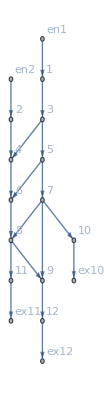

```mathematica
d2e["FG"]
```

### TIGRAN

#### large costs: 10^6

```mathematica
d2e["FG"]
```

-Graphics-

```mathematica
critNoSplt["jtvars"]
```

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critNoSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Simplifying :
{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1≤25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49&&22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19≤22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001,(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)}

$Aborted

```mathematica
ZAnd[jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1≤25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49&&22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19≤22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001,ReverseSortBy[Simplify`SimplifyCount][(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)]]//AbsoluteTiming
```

{314.231,(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt28&&0==jt29&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt28&&0==jt29&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt28/11&&0==jt29&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt28/11&&0==jt29&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt28/11&&0==jt29&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt28/11&&0==jt29&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt30/41&&0==jt32&&0==-jt33/41&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&22000+u19==22000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-jt33&&0==-jt34/11&&0==jt37/40&&0==-jt41/11&&0==jt42/40&&0==-jt44/11&&0==jt45/29&&0==-jt47/11&&0==jt48&&0==-jt49/29&&0==-4000/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&22000+u19==22000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==-jt33&&0==-jt34/11&&0==(2 jt37)/17&&0==jt41&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&11000+jt49==11000&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-jt33&&0==-jt34/11&&0==(2 jt37)/17&&0==jt41&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&11000+jt49==11000&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt49==11000&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt16&&0==-200+jt17&&0==-2200/3+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==jt37/3&&0==jt42/15&&0==-jt44/11&&0==jt45/4&&0==-jt47/11&&0==jt48&&0==-600+u1/9&&2200/3==2200/3+jt41&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==2200/3&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&u19==-3803/3&&11200/3≥11200/3+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&33400/3+jt30≤8400+jt30&&62197/3+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==jt41&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt27==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&u19==-3001&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt28/11&&0==jt29&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt30)/41&&0==jt32&&0==-(2 jt33)/41&&0==-jt34/11&&0==(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==(2 jt42)/19&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==jt41&&0==(2 jt42)/41&&0==-jt44/11&&0==(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&u19==-3001&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==-2200/3+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==jt37/3&&0==jt42/15&&0==-jt44/11&&0==jt45/4&&0==-jt47/11&&0==jt48&&0==-600+u1/9&&2200/3==2200/3+jt41&&jt10==0&&jt11==0&&jt17==200&&jt27==0&&jt28==0&&jt29==2200/3&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&u19==-3803/3&&11200/3≥11200/3+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&33400/3+jt30≤8400+jt30&&62197/3+2 jt30≤22000+2 jt30)||(0==-27250/27+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==-jt33&&0==250/27-jt32/11-jt34/11&&0==1025/108-jt32/40+jt37/40&&0==250/27-jt41/11&&0==1025/108+1/40 (-10250/27+jt32)-jt32/40+jt42/40&&0==-jt44/11&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29+jt45/29&&0==-jt47/11&&0==jt48&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29-jt49/29&&0==-100000/567+1/21 (-2750/27+jt32)-jt32/21+u1/21&&jt10==0&&jt11==250/27&&jt16==0&&jt17==0&&jt27==0&&jt30==0&&22000+3 (2750/27-jt32)+2 (-10250/27+jt32)+jt32+u19==200750/9&&0≥jt32&&302500/27≥286750/27+2 (2750/27-jt32)+2 jt32&&2750/27-jt32≥0&&-10250/27+jt32≥0&&jt32≥0&&-2000≤-44500/27+4 (2750/27-jt32)+2 (-10250/27+jt32)+2 jt32≤2001&&20000≤542000/27+4 (2750/27-jt32)+4 jt32≤24001)||(0==-27250/27+jt18&&0==jt19&&0==-jt22&&0==-jt28&&0==jt29&&0==-jt33&&0==-2750/27+jt32+jt34&&0==1250/9+1/2 (2750/27-jt32)+jt37/2&&0==-2750/27+jt41&&0==jt42/27&&0==jt44&&0==2750/729+1/27 (-2750/27+jt32)-jt32/27+jt45/27&&0==jt47&&0==jt48&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29-jt49/29&&0==-100000/567+1/21 (-2750/27+jt32)-jt32/21+u1/21&&jt10==0&&jt11==250/27&&jt16==0&&jt17==0&&jt27==0&&jt30==0&&200500/9+4 (2750/27-jt32)+3 (-10250/27+jt32)+jt32+u19==200750/9&&0≥jt32&&302500/27≥101500/9+3 (2750/27-jt32)+2 (-10250/27+jt32)+jt32&&2750/27-jt32≥0&&-10250/27+jt32≥0&&jt32≥0&&-2000≤-44500/27+4 (2750/27-jt32)+2 (-10250/27+jt32)+2 jt32≤2001&&20000≤544750/27+3 (2750/27-jt32)+3 jt32≤24001)||(0==-27250/27+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==250/27-jt32/11-jt34/11&&0==1025/108-jt32/40+jt37/40&&0==250/27-jt41/11&&0==1025/108+1/40 (-10250/27+jt32)-jt32/40+jt42/40&&0==-jt44/11&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29+jt45/29&&0==-jt47/11&&0==jt48&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29-jt49/29&&0==-100000/567+1/21 (-2750/27+jt32)-jt32/21+u1/21&&jt10==0&&jt11==250/27&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&22000+3 (2750/27-jt32)+2 (-10250/27+jt32)+jt32+u19==200750/9&&0≥jt32&&302500/27≥286750/27+2 (2750/27-jt32)+2 jt32&&2750/27-jt32≥0&&-10250/27+jt32≥0&&jt32≥0&&-2000≤-44500/27+4 (2750/27-jt32)+2 (-10250/27+jt32)+2 jt32≤2001&&20000≤542000/27+4 (2750/27-jt32)+4 jt32≤24001)||(0==-27250/27+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==-2750/27+jt32+jt34&&0==1250/9+1/2 (2750/27-jt32)+jt37/2&&0==jt42/27&&0==jt44&&0==2750/729+1/27 (-2750/27+jt32)-jt32/27+jt45/27&&0==jt47&&0==jt48&&0==10250/783+1/29 (-10250/27+jt32)-jt32/29-jt49/29&&0==-100000/567+1/21 (-2750/27+jt32)-jt32/21+u1/21&&jt10==0&&jt11==250/27&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==-2750/27+jt32+jt41&&200500/9+4 (2750/27-jt32)+3 (-10250/27+jt32)+jt32+u19==200750/9&&0≥jt32&&302500/27≥101500/9+3 (2750/27-jt32)+2 (-10250/27+jt32)+jt32&&2750/27-jt32≥0&&-10250/27+jt32≥0&&jt32≥0&&-2000≤-44500/27+4 (2750/27-jt32)+2 (-10250/27+jt32)+2 jt32≤2001&&20000≤544750/27+3 (2750/27-jt32)+3 jt32≤24001)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==-(2 jt33)/41&&0==-jt32/11-jt34/11&&0==-(2 jt32)/17+(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&0≥jt32&&-jt32≥0&&jt32≥0&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==-jt32/11-jt34/11&&0==-(2 jt32)/17+(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&0≥jt32&&-jt32≥0&&jt32≥0&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==jt32+jt34&&0==-(2 jt32)/17+(2 jt37)/17&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==-2000/11+(2 u19)/11&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==jt32+jt44&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&0≥jt32&&-jt32≥0&&jt32≥0&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==-(2 jt33)/41&&0==-jt32/11-jt34/11&&0==-(2 jt32)/17+(2 jt37)/17&&0==jt44&&0==jt47&&0==jt41+jt48&&0==-4000/9+u1/9&&0==2000/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&11000+jt49==11000+jt41&&0≥jt32&&-jt32≥0&&jt32≥0&&-jt41≥0&&jt41≥0&&11000+jt41≥11000+jt41&&4000+jt41≤5000&&23000+jt41≤22000+jt41&&25000+jt41≤25000+jt41)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==4001/52-jt32/11-jt34/11&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==4001/52-jt41/11&&0==-jt44/11&&0==164041/988+(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==59989/4836-(2 u19)/93&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-164041/104-jt42≥0&&jt42≥0&&1067981/104-jt42≤616011/52&&268015/52+jt42≤5000&&20000≤2268047/104-3 (44011/52-jt32)-3 (-164041/104+jt32)≤24001)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==-44011/52+jt32+jt34&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==jt44&&0==252063/2132-2/41 (44011/52-jt32)-(2 jt32)/41+(2 jt42)/41+(2 jt45)/41&&0==jt47&&0==jt48&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==-59989/572+(2 u19)/11&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==-44011/52+jt32+jt41&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-164041/104-jt42≥0&&jt42≥0&&1067981/104-jt42≤616011/52&&268015/52+jt42≤5000&&20000≤2268047/104-3 (44011/52-jt32)-3 (-164041/104+jt32)≤24001)||(0==-7125/7+jt18&&0==jt19&&0==-jt22&&0==-jt30/28&&0==jt32&&0==-jt33/28&&0==125/7-jt34/11&&0==jt37/27&&0==jt44&&0==jt47&&0==-1375/7+jt41+jt48&&0==-1300/21+jt41/15-jt49/15&&0==7625/14-u1/8&&jt10==0&&jt11==125/7&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&151625/7+jt41+u19==156750/7+jt41&&1375/7-jt41≥0&&-6500/7+jt41≥0&&jt41≥0&&78375/7+jt41≥73250/7+jt41&&28500/7+jt41≤5000&&156750/7+jt41≤156750/7+jt41&&180125/7+jt41≤169875/7+jt41&&20000≤153000/7+2 (-6500/7+jt41)-2 jt41≤24001)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt29/11&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==-(2 jt30)/41-(2 jt33)/41&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-200/3+jt42/15&&0==2000/19+(2 jt44)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt44&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-1000-jt44≥0&&jt44≥0&&0≤jt44&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==-jt44/11&&0==(2 jt42)/19+(2 jt45)/19&&0==-jt47/11&&0==jt48&&0==-4000/9+u1/9&&0==-6002/93-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==-jt41/11&&0==jt44&&0==(2 jt42)/19+(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt42≥0&&jt42≥0&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt16&&0==jt17&&0==-1000+jt18&&0==jt19&&0==-jt22&&0==jt32&&0==jt30/11-jt34/11&&0==(2 jt37)/17&&0==(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==(2 jt45)/19&&0==-4000/9+u1/9&&0==-3001/21-u19/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==-jt33&&jt47==0&&jt48==0&&11000+jt30+jt49==11000+jt30&&0≥jt41&&4000≥3000+jt30&&-jt30≥0&&jt30≥0&&11000+jt30≥11000+jt30&&-jt41≥0&&jt41≥0&&0≤jt41&&9000+jt30≤9000+jt30&&18999+2 jt30≤22000+2 jt30)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==4001/52-jt32/11-jt34/11&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==4001/52-jt41/11&&0==jt44&&0==164041/988+(2 jt42)/19+(2 jt45)/19&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==-42017/546+1/7 (164041/104-jt32)+1/7 (-44011/52+jt32)-u19/21&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt47==0&&jt48==0&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-164041/104-jt42≥0&&jt42≥0&&163995/8-2 (44011/52-jt32)-2 (-164041/104+jt32)≤2388025/104&&1067981/104-jt42≤616011/52&&268015/52+jt42≤5000&&-2000≤-27981/52+2 (44011/52-jt32)+2 (-164041/104+jt32)≤2001)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==4001/52-jt32/11-jt34/11&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==4001/52+(2 jt41)/19+(2 jt42)/19&&0==jt44&&0==4001/52+2/19 (-76019/104-jt41)+(2 jt41)/19+(2 jt45)/19&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==-42017/546+1/7 (164041/104-jt32)+1/7 (-44011/52+jt32)-u19/21&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt47==0&&jt48==0&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52≥jt41&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-76019/104-jt41≥0&&jt41≥0&&44011/52≤jt41&&163995/8-2 (44011/52-jt32)-2 (-164041/104+jt32)≤2388025/104&&-2000≤-27981/52+2 (44011/52-jt32)+2 (-164041/104+jt32)≤2001)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==-44011/52+jt32+jt34&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==76019/104+jt41+jt42&&0==jt44&&0==jt45&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==-42017/546+1/7 (164041/104-jt32)+1/7 (-44011/52+jt32)-u19/21&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt47==0&&jt48==0&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52≥jt41&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-76019/104-jt41≥0&&jt41≥0&&44011/52≤jt41&&1955891/104-2 (-164041/104+jt32)+2 jt32≤2388025/104&&-2000≤-27981/52+2 (44011/52-jt32)+2 (-164041/104+jt32)≤2001)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==-44011/52+jt32+jt34&&0==76019/884+2/17 (44011/52-jt32)+(2 jt37)/17&&0==jt44&&0==164041/104+jt42+jt45&&0==-83995/234+1/9 (44011/52-jt32)+1/9 (-164041/104+jt32)+u1/9&&0==-42017/546+1/7 (164041/104-jt32)+1/7 (-44011/52+jt32)-u19/21&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==-44011/52+jt32+jt41&&jt47==0&&jt48==0&&1156003/104+jt49==1156003/104&&0≥jt32&&44011/52-jt32≥0&&-164041/104+jt32≥0&&jt32≥0&&-164041/104-jt42≥0&&jt42≥0&&1955891/104-2 (-164041/104+jt32)+2 jt32≤2388025/104&&1067981/104-jt42≤616011/52&&268015/52+jt42≤5000&&-2000≤-27981/52+2 (44011/52-jt32)+2 (-164041/104+jt32)≤2001)||(0==-56001/52+jt18&&0==jt19&&0==-jt22&&0==-jt33&&0==4001/52-jt32/11-jt34/11&&0==34507/676-jt32/26+jt37/26&&0==4001/52-jt41/11&&0==-jt44/11&&0==164041/1508+1/29 (-34507/26+jt32)-jt32/29+jt42/29+jt45/29&&0==-jt47/11&&0==jt48&&0==164041/1508+1/29 (-34507/26+jt32)-jt32/29+1/29 (-95027/52-jt42)+jt42/29-jt49/29&&0==-952/13+1/21 (-44011/52+jt32)-jt32/21+1/21 (-95027/52-jt42)+jt42/21+u1/21&&jt10==0&&jt11==4001/52&&jt16==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&22000+3 (44011/52-jt32)+2 (-34507/26+jt32)+jt32+u19==590503/26&&0≥jt32&&564995/52≥251493/26+2 (44011/52-jt32)+2 jt32&&44011/52-jt32≥0&&-34507/26+jt32≥0&&jt32≥0&&-95027/52-jt42≥0&&jt42≥0&&130246/13-jt42≤616011/52&&268015/52+jt42≤5000&&-2000≤-166035/26+4 (44011/52-jt32)+2 (-34507/26+jt32)+2 jt32-2 (-95027/52-jt42)-2 jt42≤2001&&20000≤786927/52+4 (44011/52-jt32)+4 jt32-3 (-95027/52-jt42)-3 jt42≤24001)||(0==-jt16&&0==-18003/41+jt17&&0==-16996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-9803/123-jt30/15-jt33/15&&0==-6001/41+1/11 (49015/41+jt30)-jt34/11&&0==16996/123+1/3 (-16996/41+jt30)-jt30/3+jt37/3&&0==-16251/41+jt41/4&&0==jt44&&0==131015/41+jt47+jt48&&0==-24890/41+1/9 (-16996/41+jt30)-jt30/9+u1/9&&0==-1603/123-u19/30&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&367993/41+jt30+jt49==449993/41+jt30&&-66011/41≥-66011/41-jt47&&0≥jt47&&139996/41≥3000+jt30&&-49015/41-jt30≥0&&-16996/41+jt30≥0&&jt30≥0&&449993/41+jt30≥449993/41+jt30&&-131015/41-jt47≥0&&jt47≥0&&446006/41+jt30≤297995/41+jt30&&867967/41+2 jt30≤834982/41+2 jt30&&20000≤769012/41-3 (-16996/41+jt30)+3 jt30≤24001)||(0==-jt16&&0==-12003/52+jt17&&0==-8999/13+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-4001/52-(2 jt30)/41-(2 jt33)/41&&0==-4001/52+1/11 (164041/104+jt30)-jt34/11&&0==-76019/884-(2 jt30)/17+2/17 (76019/104+jt30)+(2 jt37)/17&&0==-17001/52+jt41/4&&0==jt44&&0==112015/52+jt47+jt48&&0==-41335/78-jt30/9+1/9 (76019/104+jt30)+u1/9&&0==-268093/4836-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&1131997/104+jt30+jt49==595993/52+jt30&&-44011/52≥-44011/52-jt47&&0≥jt47&&47999/13≥3000+jt30&&-164041/104-jt30≥0&&jt30≥0&&76019/104+jt30≥0&&595993/52+jt30≥595993/52+jt30&&-112015/52-jt47≥0&&jt47≥0&&940001/104+jt30≤940001/104+jt30&&267989/13+2 jt30≤561991/26+2 jt30&&20000≤2308057/104+3 jt30-3 (76019/104+jt30)≤24001)||(0==-jt16&&0==-8999/13+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-4001/52-(2 jt30)/41-(2 jt33)/41&&0==-4001/52+1/11 (164041/104+jt30)-jt34/11&&0==-76019/884-(2 jt30)/17+2/17 (76019/104+jt30)+(2 jt37)/17&&0==-17001/52+jt41/4&&0==jt44&&0==112015/52+jt47+jt48&&0==-41335/78-jt30/9+1/9 (76019/104+jt30)+u1/9&&0==-268093/4836-(2 u19)/93&&jt10==0&&jt11==0&&jt17==12003/52&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&1131997/104+jt30+jt49==595993/52+jt30&&-44011/52≥-44011/52-jt47&&0≥jt47&&47999/13≥3000+jt30&&-164041/104-jt30≥0&&jt30≥0&&76019/104+jt30≥0&&595993/52+jt30≥595993/52+jt30&&-112015/52-jt47≥0&&jt47≥0&&940001/104+jt30≤940001/104+jt30&&267989/13+2 jt30≤561991/26+2 jt30&&20000≤2308057/104+3 jt30-3 (76019/104+jt30)≤24001)||(0==-jt16&&0==-16996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-9803/123-jt30/15-jt33/15&&0==-6001/41+1/11 (49015/41+jt30)-jt34/11&&0==16996/123+1/3 (-16996/41+jt30)-jt30/3+jt37/3&&0==-16251/41+jt41/4&&0==jt44&&0==131015/41+jt47+jt48&&0==-24890/41+1/9 (-16996/41+jt30)-jt30/9+u1/9&&0==-1603/123-u19/30&&jt10==0&&jt11==0&&jt17==18003/41&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&367993/41+jt30+jt49==449993/41+jt30&&-66011/41≥-66011/41-jt47&&0≥jt47&&139996/41≥3000+jt30&&-49015/41-jt30≥0&&-16996/41+jt30≥0&&jt30≥0&&449993/41+jt30≥449993/41+jt30&&-131015/41-jt47≥0&&jt47≥0&&446006/41+jt30≤297995/41+jt30&&867967/41+2 jt30≤834982/41+2 jt30&&20000≤769012/41-3 (-16996/41+jt30)+3 jt30≤24001)||(0==-jt16&&0==-18003/41+jt17&&0==-16996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-9803/123-jt30/15-jt33/15&&0==-6001/41+1/11 (49015/41+jt30)-jt34/11&&0==16996/123+1/3 (-16996/41+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==66011/41+jt41+jt48&&0==-24890/41+1/9 (-16996/41+jt30)-jt30/9+u1/9&&0==-1603/123-u19/30&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&367993/41+jt30+jt49==384989/41+jt30+jt41&&139996/41≥3000+jt30&&-49015/41-jt30≥0&&-16996/41+jt30≥0&&jt30≥0&&-66011/41-jt41≥0&&jt41≥0&&16996/41+jt41≥0&&384989/41+jt30+jt41≥384989/41+jt30+jt41&&446006/41+jt30≤297995/41+jt30&&139996/41+jt41≤5000&&975985/41+jt41≤975985/41+jt41&&802963/41+2 jt30+jt41≤769978/41+2 jt30+jt41&&20000≤769012/41-3 (-16996/41+jt30)+3 jt30≤24001)||(0==-jt16&&0==-1667/4+jt17&&0==-1333/3+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-289/4-jt30/15-jt33/15&&0==-1667/12+1/11 (4335/4+jt30)-jt34/11&&0==1333/9+1/3 (-1333/3+jt30)-jt30/3+jt37/3&&0==-4667/12+jt41/4&&0==jt44&&0==12335/4+jt47+jt48&&0==-20335/12+jt49&&0==-42337/126+1/21 (1333/3-jt30)+1/21 (4335/4+jt30)+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&135665/6+3 (-1333/3+jt30)-jt30+u19==40999/2+2 jt30&&-18337/12≥-18337/12-jt47&&0≥jt47&&10333/3≥3000+jt30&&-4335/4-jt30≥0&&-1333/3+jt30≥0&&jt30≥0&&132331/12+jt30≥64333/6+jt30&&-12335/4-jt47≥0&&jt47≥0&&126337/12+jt30≤87665/12+jt30&&40999/2+2 jt30≤40999/2+2 jt30&&-2000≤35675/6+2 (-4335/4-jt30)+4 (-1333/3+jt30)-2 jt30≤2001&&20000≤98337/4+3 (-4335/4-jt30)+3 (-1333/3+jt30)≤24001)||(0==-jt16&&0==-12003/52+jt17&&0==-8999/13+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-4001/52-(2 jt30)/41-(2 jt33)/41&&0==-4001/52+1/11 (164041/104+jt30)-jt34/11&&0==-76019/884-(2 jt30)/17+2/17 (76019/104+jt30)+(2 jt37)/17&&0==jt44&&0==jt47&&0==44011/52+jt41+jt48&&0==-41335/78-jt30/9+1/9 (76019/104+jt30)+u1/9&&0==-268093/4836-(2 u19)/93&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&1131997/104+jt30+jt49==527989/52+jt30+jt41&&47999/13≥3000+jt30&&-164041/104-jt30≥0&&jt30≥0&&76019/104+jt30≥0&&-44011/52-jt41≥0&&-76019/104+jt41≥0&&jt41≥0&&527989/52+jt30+jt41≥527989/52+jt30+jt41&&940001/104+jt30≤940001/104+jt30&&47999/13+jt41≤5000&&2435959/104+jt41≤2435959/104+jt41&&250988/13+2 jt30+jt41≤527989/26+2 jt30+jt41&&20000≤2308057/104+3 jt30-3 (76019/104+jt30)≤24001)||(0==-jt16&&0==-6003/41+jt17&&0==-32996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-14203/123-jt30/15-jt33/15&&0==-2001/41+1/11 (71015/41+jt30)-jt34/11&&0==-49004/123-jt30/3+1/3 (49004/41+jt30)+jt37/3&&0==jt44&&0==jt47&&0==22011/41+jt41+jt48&&0==38999/41-u1/5&&0==-2001/41-u19/41&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&477993/41+jt30+jt49==428989/41+jt30+jt41&&155996/41≥3000+jt30&&-71015/41-jt30≥0&&jt30≥0&&49004/41+jt30≥0&&-22011/41-jt41≥0&&-49004/41+jt41≥0&&jt41≥0&&428989/41+jt30+jt41≥428989/41+jt30+jt41&&399995/41+jt30≤399995/41+jt30&&155996/41+jt41≤5000&&1013974/41+jt41≤953985/41+jt41&&846952/41+2 jt30+jt41≤857978/41+2 jt30+jt41&&20000≤918008/41+2 jt30-2 (49004/41+jt30)≤24001)||(0==-jt16&&0==-32996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-14203/123-jt30/15-jt33/15&&0==-2001/41+1/11 (71015/41+jt30)-jt34/11&&0==-49004/123-jt30/3+1/3 (49004/41+jt30)+jt37/3&&0==jt44&&0==jt47&&0==22011/41+jt41+jt48&&0==38999/41-u1/5&&0==-2001/41-u19/41&&jt10==0&&jt11==0&&jt17==6003/41&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&477993/41+jt30+jt49==428989/41+jt30+jt41&&155996/41≥3000+jt30&&-71015/41-jt30≥0&&jt30≥0&&49004/41+jt30≥0&&-22011/41-jt41≥0&&-49004/41+jt41≥0&&jt41≥0&&428989/41+jt30+jt41≥428989/41+jt30+jt41&&399995/41+jt30≤399995/41+jt30&&155996/41+jt41≤5000&&1013974/41+jt41≤953985/41+jt41&&846952/41+2 jt30+jt41≤857978/41+2 jt30+jt41&&20000≤918008/41+2 jt30-2 (49004/41+jt30)≤24001)||(0==-jt16&&0==-8999/13+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-4001/52-(2 jt30)/41-(2 jt33)/41&&0==-4001/52+1/11 (164041/104+jt30)-jt34/11&&0==-76019/884-(2 jt30)/17+2/17 (76019/104+jt30)+(2 jt37)/17&&0==jt44&&0==jt47&&0==44011/52+jt41+jt48&&0==-41335/78-jt30/9+1/9 (76019/104+jt30)+u1/9&&0==-268093/4836-(2 u19)/93&&jt10==0&&jt11==0&&jt17==12003/52&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&1131997/104+jt30+jt49==527989/52+jt30+jt41&&47999/13≥3000+jt30&&-164041/104-jt30≥0&&jt30≥0&&76019/104+jt30≥0&&-44011/52-jt41≥0&&-76019/104+jt41≥0&&jt41≥0&&527989/52+jt30+jt41≥527989/52+jt30+jt41&&940001/104+jt30≤940001/104+jt30&&47999/13+jt41≤5000&&2435959/104+jt41≤2435959/104+jt41&&250988/13+2 jt30+jt41≤527989/26+2 jt30+jt41&&20000≤2308057/104+3 jt30-3 (76019/104+jt30)≤24001)||(0==-jt16&&0==-1333/3+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-289/4-jt30/15-jt33/15&&0==-1667/12+1/11 (4335/4+jt30)-jt34/11&&0==1333/9+1/3 (-1333/3+jt30)-jt30/3+jt37/3&&0==-4667/12+jt41/4&&0==jt44&&0==12335/4+jt47+jt48&&0==-20335/12+jt49&&0==-42337/126+1/21 (1333/3-jt30)+1/21 (4335/4+jt30)+u1/21&&jt10==0&&jt11==0&&jt17==1667/4&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&135665/6+3 (-1333/3+jt30)-jt30+u19==40999/2+2 jt30&&-18337/12≥-18337/12-jt47&&0≥jt47&&10333/3≥3000+jt30&&-4335/4-jt30≥0&&-1333/3+jt30≥0&&jt30≥0&&132331/12+jt30≥64333/6+jt30&&-12335/4-jt47≥0&&jt47≥0&&126337/12+jt30≤87665/12+jt30&&40999/2+2 jt30≤40999/2+2 jt30&&-2000≤35675/6+2 (-4335/4-jt30)+4 (-1333/3+jt30)-2 jt30≤2001&&20000≤98337/4+3 (-4335/4-jt30)+3 (-1333/3+jt30)≤24001)||(0==-jt16&&0==-16996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-9803/123-jt30/15-jt33/15&&0==-6001/41+1/11 (49015/41+jt30)-jt34/11&&0==16996/123+1/3 (-16996/41+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==66011/41+jt41+jt48&&0==-24890/41+1/9 (-16996/41+jt30)-jt30/9+u1/9&&0==-1603/123-u19/30&&jt10==0&&jt11==0&&jt17==18003/41&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&367993/41+jt30+jt49==384989/41+jt30+jt41&&139996/41≥3000+jt30&&-49015/41-jt30≥0&&-16996/41+jt30≥0&&jt30≥0&&-66011/41-jt41≥0&&jt41≥0&&16996/41+jt41≥0&&384989/41+jt30+jt41≥384989/41+jt30+jt41&&446006/41+jt30≤297995/41+jt30&&139996/41+jt41≤5000&&975985/41+jt41≤975985/41+jt41&&802963/41+2 jt30+jt41≤769978/41+2 jt30+jt41&&20000≤769012/41-3 (-16996/41+jt30)+3 jt30≤24001)||(0==-jt16&&0==-1667/4+jt17&&0==-1333/3+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-289/4-jt30/15-jt33/15&&0==-1667/12+1/11 (4335/4+jt30)-jt34/11&&0==1333/9+1/3 (-1333/3+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==18337/12+jt41+jt48&&0==-1667/12-jt41+jt49&&0==-9223/28+1/21 (1333/3-jt30)+1/21 (4335/4+jt30)+1/21 (-1667/12-jt41)+jt41/21+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&126331/6+3 (-1333/3+jt30)-jt30+jt41+u19==113663/6+2 jt30+jt41&&10333/3≥3000+jt30&&-4335/4-jt30≥0&&-1333/3+jt30≥0&&jt30≥0&&-18337/12-jt41≥0&&jt41≥0&&1667/12+jt41≥0&&113663/12+jt30+jt41≥18333/2+jt30+jt41&&126337/12+jt30≤87665/12+jt30&&10333/3+jt41≤5000&&141665/6+jt41≤141665/6+jt41&&113663/6+2 jt30+jt41≤113663/6+2 jt30+jt41&&-2000≤5668+2 (-4335/4-jt30)+4 (-1333/3+jt30)-2 jt30-2 jt41+2 (1667/12+jt41)≤2001&&20000≤48335/2+3 (-4335/4-jt30)+3 (-1333/3+jt30)-3 jt41+3 (1667/12+jt41)≤24001)||(0==-jt16&&0==-12003/41+jt17&&0==-24996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-3803/123-jt30/15-jt33/15&&0==-4001/41+1/11 (19015/41+jt30)-jt34/11&&0==8332/41+1/3 (-24996/41+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==44011/41+jt41+jt48&&0==-20203/123+1/15 (24996/41-jt30)+1/15 (19015/41+jt30)+jt41/15-jt49/15&&0==-110007/287+u1/21&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&800985/41+2 (-24996/41+jt30)+jt41+u19==813978/41+2 jt30+jt41&&147996/41≥3000+jt30&&-19015/41-jt30≥0&&-24996/41+jt30≥0&&jt30≥0&&-44011/41-jt41≥0&&-57004/41+jt41≥0&&jt41≥0&&406989/41+jt30+jt41≥324989/41+jt30+jt41&&535021/41+jt30≤307995/41+jt30&&147996/41+jt41≤5000&&27000+jt41≤923985/41+jt41&&813978/41+2 jt30+jt41≤813978/41+2 jt30+jt41&&-2000≤132033/41+2 (-24996/41+jt30)-2 jt30≤2001&&20000≤1022030/41+2 (-19015/41-jt30)+2 (-24996/41+jt30)+2 (-57004/41+jt41)-2 jt41≤24001)||(0==-jt16&&0==-24996/41+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-3803/123-jt30/15-jt33/15&&0==-4001/41+1/11 (19015/41+jt30)-jt34/11&&0==8332/41+1/3 (-24996/41+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==44011/41+jt41+jt48&&0==-20203/123+1/15 (24996/41-jt30)+1/15 (19015/41+jt30)+jt41/15-jt49/15&&0==-110007/287+u1/21&&jt10==0&&jt11==0&&jt17==12003/41&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&800985/41+2 (-24996/41+jt30)+jt41+u19==813978/41+2 jt30+jt41&&147996/41≥3000+jt30&&-19015/41-jt30≥0&&-24996/41+jt30≥0&&jt30≥0&&-44011/41-jt41≥0&&-57004/41+jt41≥0&&jt41≥0&&406989/41+jt30+jt41≥324989/41+jt30+jt41&&535021/41+jt30≤307995/41+jt30&&147996/41+jt41≤5000&&27000+jt41≤923985/41+jt41&&813978/41+2 jt30+jt41≤813978/41+2 jt30+jt41&&-2000≤132033/41+2 (-24996/41+jt30)-2 jt30≤2001&&20000≤1022030/41+2 (-19015/41-jt30)+2 (-24996/41+jt30)+2 (-57004/41+jt41)-2 jt41≤24001)||(0==-jt16&&0==-1333/3+jt18&&0==jt19/4&&0==-jt22&&0==jt32&&0==-289/4-jt30/15-jt33/15&&0==-1667/12+1/11 (4335/4+jt30)-jt34/11&&0==1333/9+1/3 (-1333/3+jt30)-jt30/3+jt37/3&&0==jt44&&0==jt47&&0==18337/12+jt41+jt48&&0==-1667/12-jt41+jt49&&0==-9223/28+1/21 (1333/3-jt30)+1/21 (4335/4+jt30)+1/21 (-1667/12-jt41)+jt41/21+u1/21&&jt10==0&&jt11==0&&jt17==1667/4&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&126331/6+3 (-1333/3+jt30)-jt30+jt41+u19==113663/6+2 jt30+jt41&&10333/3≥3000+jt30&&-4335/4-jt30≥0&&-1333/3+jt30≥0&&jt30≥0&&-18337/12-jt41≥0&&jt41≥0&&1667/12+jt41≥0&&113663/12+jt30+jt41≥18333/2+jt30+jt41&&126337/12+jt30≤87665/12+jt30&&10333/3+jt41≤5000&&141665/6+jt41≤141665/6+jt41&&113663/6+2 jt30+jt41≤113663/6+2 jt30+jt41&&-2000≤5668+2 (-4335/4-jt30)+4 (-1333/3+jt30)-2 jt30-2 jt41+2 (1667/12+jt41)≤2001&&20000≤48335/2+3 (-4335/4-jt30)+3 (-1333/3+jt30)-3 jt41+3 (1667/12+jt41)≤24001)}

```mathematica
ZAnd[jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1≤25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49&&22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19≤22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001,Sort[(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)]]//AbsoluteTiming
```

{1340.2,(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt30/22&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt30/22&&0==-jt45/11&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt33/22&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt33/22&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt30/22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt33/22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==1000-jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt30)/22&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt30)/22&&0==(3 jt45)/11&&0==-jt47&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt33)/22&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt33)/22&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt44)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt44)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-jt47&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt30)/22&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt33)/22&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==(3 jt49)/22&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&0==9003/5+(3 u19)/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt30/22&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt30/22&&0==-jt45/11&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt33/22&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt33/22&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt30/22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-1000+jt18&&0==-jt22&&0==-jt33/22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-jt49/22&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==-3001/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-1000+jt18&&0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000-jt30/22&&1000==1000+jt34/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000-jt33/22&&1000==1000+jt34/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000+jt34/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt30/22&&1000==1000-jt45/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt33/22&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt44/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt44/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22&&0==-jt47&&0==-3001-u19&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt47&&1000==1000-jt29/11&&1000==1000-jt30/22&&1000==1000-jt45/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt22&&0==-jt47&&1000==1000-jt29/11&&1000==1000-jt33/22&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0)||(0==-jt22&&0==-jt47&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22&&0==-jt47&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==1999/5-u19/5&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==40001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&1000==18001/15+u19/15&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22/4&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0)||(0==-jt22/4&&0==-jt45&&0==-jt47&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&4000==7001+u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt27==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt11==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt11==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt10==0&&0==-jt22&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt11==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt28==0&&jt11==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&0==jt27/3&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt17==0&&jt19==0&&jt11==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&0==-3001/5-u19/5&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&0==-jt29/11&&0==-jt45/11&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&0==3001/15+u19/15&&jt29==0&&0==-jt45&&0==-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&0==jt34/11&&jt33==0&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt11==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&0==jt34/11&&jt29==0&&0==-jt45&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt11==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&0==-1000+jt18&&jt19==0&&0==-jt17/3&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==-4000/9+u1/9&&jt33==0&&jt34==0&&0==-jt29/11&&0==-jt45/11&&0==3001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&0==-jt44/11&&jt11==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==-jt49&&jt44==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&jt34==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt30==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==-jt49&&jt44==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt33==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt49==0)||(jt10==0&&0==-jt22/4&&jt16==0&&jt28==0&&jt11==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&jt34==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt17==0&&jt19==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt27==0&&jt19==0&&jt17==0&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&0==1000-jt18&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt18==1000&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&1000==1999/5-u19/5&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&1000==18001/15+u19/15&&jt29==0&&0==-jt45&&1000==1000-jt49/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&1000==1000+jt34/11&&jt33==0&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==1000+jt48/11&&jt37==0&&jt41==0&&jt42==0&&jt18==1000&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&1000==1000+jt34/11&&jt29==0&&0==-jt45&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt18==1000&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22&&jt11==0&&jt28==0&&jt19==0&&jt17==0&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&1000==5000/9+u1/9&&jt33==0&&jt34==0&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==40001/37+u19/37&&jt37==0&&jt41==0&&jt42==0&&1000==1000-jt44/11&&jt18==1000&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt17==0&&jt28==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&0==jt27/3&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt28==0&&jt17==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&4000==7001+u19&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&0==-3001-u19&&jt29==0&&0==-jt45&&0==-jt49&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&0==jt34&&jt33==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-jt48&&jt37==0&&jt41==0&&jt42==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt17==0&&jt19==0&&jt18==1000&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000-u1&&jt33==0&&jt34==0&&jt29==0&&0==-jt45&&0==-3001-u19&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==-jt49&&jt44==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&0==9003/5+(3 u19)/5&&0==4000/3-u1/3&&jt33==0&&jt34==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt30==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==-jt49&&jt44==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&0==-3001/5-u19/5&&jt29==0&&0==-jt45&&0==(3 jt49)/22&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt33==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&0==-(3 jt34)/11&&jt33==0&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-(3 jt48)/11&&jt37==0&&jt41==0&&jt42==0&&jt17==0&&0==3001+u19&&jt44==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt48==0&&jt17==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&0==-(3 jt34)/11&&jt29==0&&0==-jt45&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&jt48==0&&jt44==0&&jt17==0&&jt49==0)||(jt16==0&&jt10==0&&0==-jt22/4&&jt11==0&&jt28==0&&jt19==0&&0==750-(3 jt18)/4&&jt32==0&&jt27==0&&0==-jt47&&jt30==0&&0==4000/3-u1/3&&jt33==0&&jt34==0&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-9003/37-(3 u19)/37&&jt37==0&&jt41==0&&jt42==0&&0==(3 jt44)/11&&jt17==0&&jt48==0&&jt49==0)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==1000-jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==1000-jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt44)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt44)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==(3 jt45)/11&&0==-jt47&&0==-jt48&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt45&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==-(3 jt34)/11&&0==-jt47&&0==-(3 jt48)/11&&0==4000/3-u1/3&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt44/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-jt48&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt45&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-1000+jt18&&0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt45&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt44/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000+jt34/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt44/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&0==-jt48&&1000==1000-jt29/11&&1000==1000-jt45/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22&&0==-jt47&&1000==1000+jt34/11&&1000==1000+jt48/11&&1000==5000/9+u1/9&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt34&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==-jt45&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt22/4&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt49==0&&22000+u19≤22000&&-2000≤-1000-u19≤2001&&20000≤21000-u19≤24001)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==jt34/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==-jt42&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==-jt29/11&&0==-jt45/11&&0==-jt47&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==-jt42&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==250-jt42/4&&0==jt48/11&&0==-4000/9+u1/9&&0==4001/41+1/41 (-1000-jt44)+jt44/41+u19/41&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==-jt17/3&&0==-1000+jt18&&0==-jt22/4&&0==jt34/11&&0==-jt47&&0==jt48/11&&0==-4000/9+u1/9&&0==3001/37+u19/37&&jt10==0&&jt11==0&&jt16==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==1000-jt18&&0==-jt22&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==1000-jt18&&0==-jt22&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==1000-jt18&&0==-jt22&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==1000-jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==1000-jt18&&0==-jt22&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==jt34&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==1000-jt42&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==-1000-jt45&&jt44==-3001+jt44-u19&&jt47==0&&jt49==0&&0≥jt44&&-1000-jt44≥0&&jt44≥0&&0≤jt44)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt45&&0==-jt47&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==-jt42&&jt41==-3001+jt41-u19&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&jt41≥0&&0≤jt41)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&0==-3001-u19&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==jt27/3&&0==-jt47&&0==-jt48&&0==4000-u1&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==-jt45&&jt42==-3001+jt42-u19&&jt44==0&&jt49==0&&-jt42≥0&&jt42≥0&&11000-jt42≤11000&&4000+jt42≤5000)||(0==750-(3 jt18)/4&&0==-jt22/4&&0==(3 jt29)/11&&0==-(3 jt34)/11&&0==(3 jt45)/11&&0==-jt47&&0==4000/3-u1/3&&0==-9003/37-(3 u19)/37&&jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt19==0&&jt27==0&&jt28==0&&jt30==0&&jt32==0&&jt33==0&&jt37==0&&jt41==-jt42&&jt44==0&&jt48==0&&jt49==0&&0≥jt41&&-jt41≥0&&

```mathematica
Sort[(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)]
```

(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||jt48==0)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)

Simplifying :
{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&5000+8 jt10+jt19+jt29+jt30+u1≤9 jt17+9 jt18+jt22+jt34+jt37&&21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1≤25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49&&22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19≤22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001,(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||jt48==0)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)}

$Aborted

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1005000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-5000&&-25000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤975000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 219.435 seconds to terminate

Simplifying :
{{True,True},(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-3001≤u19≤0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&3001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-3001≤u19≤0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&3001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 2.06022 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 0.717492 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 0.056643 seconds to terminate

Simplifying :
{{True,-3001≤u19≤0},True}

Iterative DNF convertion took 0.00001 seconds to terminate

Simplifying :
{{True,-3001≤u19≤0},True}

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{223.302,Null}

```mathematica
critNoSplt["AssoCritical"]
```

<|u1→4000,u2→3000,u3→4000,u4→3000,u5→3000,u6→3000,u7→3000,u8→2000,u9→3000,u10→2000,u11→2000,u12→2000,u13→2000,u14→1000,u15→2000,u16→1000,u17→1000,u18→1000,u19→-2974,u20→-2974,u21→1000,u22→0,u23→-2974,u24→-2974,u25→1000,u26→0,u27→-2974,u28→-2974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→4000,u36→4000,u37→4000,u38→4000,j1→0,j2→1000,j3→0,j4→1000,j5→0,j6→0,j7→0,j8→1000,j9→0,j10→1000,j11→0,j12→0,j13→0,j14→1000,j15→0,j16→1000,j17→0,j18→0,j19→0,j20→0,j21→0,j22→1000,j23→0,j24→0,j25→0,j26→1000,j27→0,j28→0,j29→0,j30→1000,j31→0,j32→1000,j33→0,j34→0,j35→0,j36→1000,j37→0,j38→1000,jt1→0,jt2→1000,jt3→0,jt4→1000,jt5→0,jt6→1000,jt7→0,jt8→0,jt9→0,jt10→0,jt11→0,jt12→1000,jt13→0,jt14→0,jt15→0,jt16→0,jt17→0,jt18→1000,jt19→0,jt20→0,jt21→0,jt22→0,jt23→0,jt24→1000,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>

```mathematica
crit["jvars"]/.crit["AssoCritical"]
```

<|{1,1->3}→0,{3,1->3}→1000,{2,2->4}→0,{4,2->4}→1000,{3,3->4}→0,{4,3->4}→0,{3,3->5}→0,{5,3->5}→1000,{4,4->6}→0,{6,4->6}→1000,{5,5->6}→0,{6,5->6}→0,{5,5->7}→0,{7,5->7}→1000,{6,6->8}→0,{8,6->8}→1000,{7,7->8}→0,{8,7->8}→0,{7,7->9}→0,{9,7->9}→0,{7,7->10}→0,{10,7->10}→1000,{8,8->9}→0,{9,8->9}→0,{8,8->11}→0,{11,8->11}→1000,{9,9->12}→0,{12,9->12}→0,{10,10->ex10}→0,{ex10,10->ex10}→1000,{11,11->ex11}→0,{ex11,11->ex11}→1000,{12,12->ex12}→0,{ex12,12->ex12}→0,{en1,en1->1}→0,{1,en1->1}→1000,{en2,en2->2}→0,{2,en2->2}→1000|>

```mathematica
{B,K,cost,vars}=GetKirchhoffMatrix[critNoSplt]
```

{SparseArray[…],SparseArray[…],Function[currents$,MapThread[#1[#2]&,{KeyMap[Join[jvars$9524986,jtvars$9524986]][CostArgs$9524986]/@vars$9524986,currents$}]],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}

```mathematica
vars
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}

```mathematica
cost[vars]
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,0,0,0,0,0,j4,j5,j6,j7,j8,j9,1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1000000,1/1000000,1000000,1/1000000,1000000,1/1000000,1/1000000,1/1000000}

```mathematica
Get[dddRicardo]

Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Iterative DNF convertion took 391.2 seconds to terminate

Iterative DNF convertion took 5.99267 seconds to terminate

Iterative DNF convertion took 4.60787 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

{403.404,Null}

```mathematica
Get[dddRicardo]
(*this has large but not infinity costs on entrance and exits*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000000≤5000+8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-953000≤-44 jt10+43 jt17+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤47000&&-1000000≤46000+52 jt10-49 jt17-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&5000+4 jt10+jt27+jt28≥4 jt17+4 jt18+jt41+jt42&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&3000+3 jt10+jt19≤4 jt17+3 jt18+jt22&&3000+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5000+4 jt10+jt16+jt28≥5 jt17+4 jt18+jt22&&2000+jt10+jt16≥jt17+jt18&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (16500+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48},(35 jt10+2 (16500+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||47000+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 103.818 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt30==250+jt34&&jt32==0&&jt30+jt33==250&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt44==0&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt44==0&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&u1==3750)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt30==250+jt34&&jt32==0&&jt30+jt33==250&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==250&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt44==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt44==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt29==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)}

Iterative DNF convertion took 0.805282 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)}

Iterative DNF convertion took 0.590852 seconds to terminate

Simplifying :
{{True,True},True}

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{105.851,Null}

```mathematica
Get[dddRicardo]
(*infinity costs at entrance and exit*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
"Iterative DNF convertion took "107.29792" seconds to terminate"
"Iterative DNF convertion took "0.770732" seconds to terminate"
"Iterative DNF convertion took "0.583327" seconds to terminate"
"Iterative DNF convertion took "5.*^-6" seconds to terminate"
{109.240226,Null}
critSplt["AssoCritical"]
<|u1->3750,u2->2750,u3->3750,u4->2750,u5->2750,u6->2750,u7->2750,u8->1750,u9->2750,u10->1750,u11->1750,u12->1750,u13->1750,u14->750,u15->1750,u16->750,u17->750,u18->750,u19->750,u20->500,u21->750,u22->0,u23->750,u24->500,u25->750,u26->0,u27->500,u28->0,u29->0,u30->0,u31->0,u32->0,u33->0,u34->0,u35->3750,u36->3750,u37->3750,u38->3750,j1->0,j2->1000,j3->0,j4->1000,j5->0,j6->0,j7->0,j8->1000,j9->0,j10->1000,j11->0,j12->0,j13->0,j14->1000,j15->0,j16->1000,j17->0,j18->0,j19->0,j20->250,j21->0,j22->750,j23->0,j24->250,j25->0,j26->750,j27->0,j28->500,j29->0,j30->750,j31->0,j32->750,j33->0,j34->500,j35->0,j36->1000,j37->0,j38->1000,jt1->0,jt2->1000,jt3->0,jt4->1000,jt5->0,jt6->1000,jt7->0,jt8->0,jt9->0,jt10->0,jt11->0,jt12->1000,jt13->0,jt14->0,jt15->0,jt16->0,jt17->0,jt18->1000,jt19->0,jt20->0,jt21->0,jt22->0,jt23->0,jt24->1000,jt25->0,jt26->0,jt27->0,jt28->0,jt29->0,jt30->250,jt31->750,jt32->0,jt33->0,jt34->0,jt35->0,jt36->0,jt37->0,jt38->0,jt39->0,jt40->0,jt41->0,jt42->250,jt43->750,jt44->0,jt45->0,jt46->0,jt47->0,jt48->0,jt49->0,jt50->0,jt51->0,jt52->0,jt53->0,jt54->250,jt55->0,jt56->250,jt57->0,jt58->0,jt59->750,jt60->0,jt61->750,jt62->0,jt63->500,jt64->0|>
GetKirchhoffMatrix[critSplt]
{SparseArray[…],SparseArray[…],Function[currents$,MapThread[#1[#2]&,{KeyMap[Join[jvars$5539288,jtvars$5539288]][CostArgs$5539288]/@vars$5539288,currents$}]],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}
```

```mathematica
alpha[x_]:=1;
NonLinear[critNoSplt]
```

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1013000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-13000&&-17000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤983000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-8000≤5 jt10-5 jt17-5 jt18+u1-u19≤-3999&&20000≤6000-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||17000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||13000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11000+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt10+jt22==jt19+jt32||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt30==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt27+jt28==0||5000+4 jt10+jt27+jt28==4 (jt17+jt18))&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 205.416 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&-5001≤u19≤-1000)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt44==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)}

Iterative DNF convertion took 3.19833 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.905726 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.048229 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -5001≤u19≤-1000

Picked one value for the variable(s) {u19} {-4974} (respectively)

Max error for non-linear solution: 1.13687×10^-12

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1013000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-13000&&-17000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤983000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-8000≤5 jt10-5 jt17-5 jt18+u1-u19≤-3999&&20000≤6000-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||17000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||13000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11000+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt10+jt22==jt19+jt32||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt30==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt27+jt28==0||5000+4 jt10+jt27+jt28==4 (jt17+jt18))&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 205.436 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&-5001≤u19≤-1000)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt44==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)}

Iterative DNF convertion took 3.12396 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.868602 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.061149 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -5001≤u19≤-1000

Picked one value for the variable(s) {u19} {-4974} (respectively)

Max error for non-linear solution: 1.13687×10^-12

Iterated 2 times out of 15

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12},63,AssoNonCritical→<|u1→-4000,u2→-3000,u3→-4000,u4→-3000,u5→-3000,u6→-3000,u7→-3000,u8→-2000,u9→-3000,u10→-2000,u11→-2000,u12→-2000,u13→-2000,u14→-1000,u15→-2000,u16→-1000,u17→-1000,u18→-1000,u19→-4974,u20→-4974,u21→-1000,u22→0,u23→-4974,u24→-4974,u25→-1000,u26→0,u27→-4974,u28→-4974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→-4000,u36→-4000,u37→-4000,u38→-4000,j1→0,62,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>|>
 |  |  |  |

```mathematica
critNoSplt["AssoCritical"]
```

<|u1→4000,u2→3000,u3→4000,u4→3000,u5→3000,u6→3000,u7→3000,u8→2000,u9→3000,u10→2000,u11→2000,u12→2000,u13→2000,u14→1000,u15→2000,u16→1000,u17→1000,u18→1000,u19→-2974,u20→-2974,u21→1000,u22→0,u23→-2974,u24→-2974,u25→1000,u26→0,u27→-2974,u28→-2974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→4000,u36→4000,u37→4000,u38→4000,j1→0,j2→1000,j3→0,j4→1000,j5→0,j6→0,j7→0,j8→1000,j9→0,j10→1000,j11→0,j12→0,j13→0,j14→1000,j15→0,j16→1000,j17→0,j18→0,j19→0,j20→0,j21→0,j22→1000,j23→0,j24→0,j25→0,j26→1000,j27→0,j28→0,j29→0,j30→1000,j31→0,j32→1000,j33→0,j34→0,j35→0,j36→1000,j37→0,j38→1000,jt1→0,jt2→1000,jt3→0,jt4→1000,jt5→0,jt6→1000,jt7→0,jt8→0,jt9→0,jt10→0,jt11→0,jt12→1000,jt13→0,jt14→0,jt15→0,jt16→0,jt17→0,jt18→1000,jt19→0,jt20→0,jt21→0,jt22→0,jt23→0,jt24→1000,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>

```mathematica
Get[dddRicardo]
alpha[x_]:=1;
IsNonLinearSolution[critNoSplt][critNoSplt["AssoCritical"]]
```

EqEntryIn: True
j36==1000&&j38==1000

EqValueAuxiliaryEdges: True
u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34

EqCompCon: True
(jt1==0||1000000-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||1000000-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||4001-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||4001-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||4001+u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||4001-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||4001-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||4001+u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||1000000+u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||1000000+u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||1000000+u28-u33==0)

EqBalanceSplittingCurrents: True
j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64

EqCurrentCompCon: True
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0)

EqTransitionCompCon: True
(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0

EqPosJts: True
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0

EqSwitchingByVertex: True
u1≤1000000+u36&&u36≤u1&&u3≤1000000+u38&&u38≤u3&&u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5&&u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6&&u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11&&u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12&&u14≤u17&&u14≤4001+u19&&u14≤u21&&u17≤u14&&u17≤4001+u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤4001+u19&&u16≤u18&&u16≤4001+u23&&u16≤u25&&u18≤u16&&u18≤4001+u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤4001+u23&&u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24&&u22≤u29&&u29≤1000000+u22&&u26≤u31&&u31≤1000000+u26&&u28≤u33&&u33≤1000000+u28

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {2000.,2000.,0.,2000.,2000.,0.,2000.,2000.,0.,0.,2000.,0.,2000.,0.}
{-j1+j2+IntM[-j1+j2,1->3],-j3+j4+IntM[-j3+j4,2->4],-j5+j6+IntM[-j5+j6,3->4],-j7+j8+IntM[-j7+j8,3->5],j10-j9+IntM[j10-j9,4->6],-j11+j12+IntM[-j11+j12,5->6],-j13+j14+IntM[-j13+j14,5->7],-j15+j16+IntM[-j15+j16,6->8],-j17+j18+IntM[-j17+j18,7->8],-j19+j20+IntM[-j19+j20,7->9],-j21+j22+IntM[-j21+j22,7->10],-j23+j24+IntM[-j23+j24,8->9],-j25+j26+IntM[-j25+j26,8->11],-j27+j28+IntM[-j27+j28,9->12]}

Max error for non-linear solution: 2000.

<|u1→4000.,u2→3000.,u3→4000.,u4→3000.,u5→3000.,u6→3000.,u7→3000.,u8→2000.,u9→3000.,u10→2000.,u11→2000.,u12→2000.,u13→2000.,u14→1000.,u15→2000.,u16→1000.,u17→1000.,u18→1000.,u19→-2974.,u20→-2974.,u21→1000.,u22→0.,u23→-2974.,u24→-2974.,u25→1000.,u26→0.,u27→-2974.,u28→-2974.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→4000.,u36→4000.,u37→4000.,u38→4000.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→0.,j21→0.,j22→1000.,j23→0.,j24→0.,j25→0.,j26→1000.,j27→0.,j28→0.,j29→0.,j30→1000.,j31→0.,j32→1000.,j33→0.,j34→0.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→0.,jt31→1000.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→0.,jt43→1000.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→0.,jt55→0.,jt56→0.,jt57→0.,jt58→0.,jt59→1000.,jt60→0.,jt61→1000.,jt62→0.,jt63→0.,jt64→0.|>

```mathematica
d2eNS=Data2Equations[d2e];
```

```mathematica
d2eNS["Nrhs"]
```

{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

```mathematica
d2eNS["Nlhs"]
```

{-j1+j2+u1-u2,-j3+j4+u3-u4,-j5+j6+u5-u6,-j7+j8+u7-u8,j10-j9-u10+u9,-j11+j12+u11-u12,-j13+j14+u13-u14,-j15+j16+u15-u16,-j17+j18+u17-u18,-j19+j20+u19-u20,-j21+j22+u21-u22,-j23+j24+u23-u24,-j25+j26+u25-u26,-j27+j28+u27-u28}

```mathematica
Get[dddRicardo]
```

Get::stream: dddRicardo is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

```mathematica
F[And[AA_,B_]]:=AA
```

```mathematica
F[x==0&&x>=3&&x>=5]
```

x==0